```mathematica
/Users/warren/Documents/Princeton/EGR191/Lab 7/Mathematica Code
```

```mathematica
ClearAll
```

ClearAll

```mathematica
sol2=DSolve[{v'[t]==-u Log[(M2/M1)]-gt,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

{{v[t]→-0.199024+33.7402 t-1. gt t}}

-0.199024+33.7402 t-1. gt t

-0.199024 t+16.8701 t^2-0.5 gt t^2

33.7402-1. gt

26.0768

0.1889

0.6889

1.84838

9.81

-Graphics-

```mathematica
sol2=DSolve[{v'[t]==-u Log[((M1-M0t)/M1)]-gt,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

{{v[t]→-0.199024-1. gt t-26.0768 t Log[1.45159 (0.6889-1. M0t)]}}

-0.199024-1. gt t-26.0768 t Log[1.45159 (0.6889-1. M0t)]

-0.199024 t-0.5 gt t^2-13.0384 t^2 Log[1.45159 (0.6889-1. M0t)]

-1. gt-26.0768 Log[1.45159 (0.6889-1. M0t)]

26.0768

0.1889

0.6889

1.84838

9.81

-Graphics-

```mathematica
ClearAll
```

ClearAll

```mathematica
sol2=DSolve[{v'[t]==-u Log[((M1-M0*t)/M1)]-gt,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

{{v[t]→-0.199024+26.0768 t-1. gt t+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]}}

-0.199024+26.0768 t-1. gt t+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]

-5.0585 t+19.5576 t^2-0.5 gt t^2-1.81115 Log[1.-2.68309 t]+9.71894 t Log[1.-2.68309 t]-13.0384 t^2 Log[1.-2.68309 t]

26.0768-1. gt-26.0768/(1.-2.68309 t)+(69.9664 t)/(1.-2.68309 t)-26.0768 Log[1.-2.68309 t]

26.0768

0.1889

0.6889

1.84838

9.81

-Graphics-

{{v[t]→-0.199024+26.0768 t-4.905 t^2+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]}}

-0.199024+26.0768 t-4.905 t^2+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]

-5.0585 t+19.5576 t^2-1.635 t^3-1.81115 Log[1.-2.68309 t]+9.71894 t Log[1.-2.68309 t]-13.0384 t^2 Log[1.-2.68309 t]

26.0768-26.0768/(1.-2.68309 t)-9.81 t+(69.9664 t)/(1.-2.68309 t)-26.0768 Log[1.-2.68309 t]

26.0768

0.1889

0.6889

1.84838

9.81

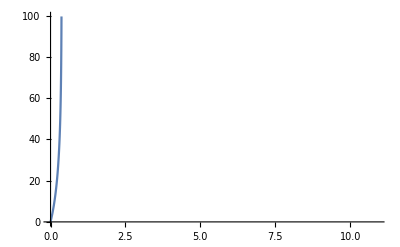

```mathematica
sol2=DSolve[{v'[t]==-u*Log[((M1-M0*t)/M1)]-g*t,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
sol2=DSolve[{v'[t]==-u*Log[((M1-M0*t)/M1)]-g*t,v[0]==0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

{{v[t]→26.0768 t-4.905 t^2+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]}}

26.0768 t-4.905 t^2+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]

-4.85947 t+19.5576 t^2-1.635 t^3-1.81115 Log[1.-2.68309 t]+9.71894 t Log[1.-2.68309 t]-13.0384 t^2 Log[1.-2.68309 t]

26.0768-26.0768/(1.-2.68309 t)-9.81 t+(69.9664 t)/(1.-2.68309 t)-26.0768 Log[1.-2.68309 t]

26.0768

0.1889

0.6889

1.84838

9.81

-Graphics-

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

DSolve[{v'[t]==9.81-5.29381 C k v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0})

{{v[t]→(-g M1 t+A1 P1 t)/M1}}

(-g M1 t+A1 P1 t)/M1

-(g t^2)/2+(A1 P1 t^2)/(2 M1)

(-g M1+A1 P1)/M1

340000.

0.0000708822

0.6889

9.81

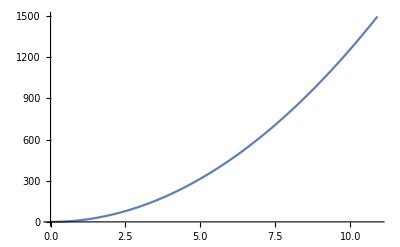

```mathematica
Clear[P1,A1,M1,g,u,M0]

sol1=DSolve[{v'[t]==(P1*A1)/M1-g,v[0]==0},v[t],t]
vsol1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[vsol1[t],t]
a1[t_]=D[vsol1[t],t]

P1=3.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M1=0.6889
g=9.81

Plot[h1[t],{t,0,10.91}]
```

{{v[t]→-1/M04.905 (1. M0 t^2-0.203874 M0 t u-0.140449 u Log[1.-1.45159 M0 t]+0.203874 M0 t u Log[1.-1.45159 M0 t])}}

-1/M04.905 (1. M0 t^2-0.203874 M0 t u-0.140449 u Log[1.-1.45159 M0 t]+0.203874 M0 t u Log[1.-1.45159 M0 t])

-1.635 t^3-(0.34445 t u)/M0+0.75 t^2 u-(0.237292 u Log[1.-1.45159 M0 t])/M0^2+(0.6889 t u Log[1.-1.45159 M0 t])/M0-0.5 t^2 u Log[1.-1.45159 M0 t]

-1/M04.905 (2. M0 t-0.203874 M0 u+(0.203874 M0 u)/(1.-1.45159 M0 t)-(0.295941 M0^2 t u)/(1.-1.45159 M0 t)+0.203874 M0 u Log[1.-1.45159 M0 t])

26.0768

0.1889

0.6889

1.84838

9.81

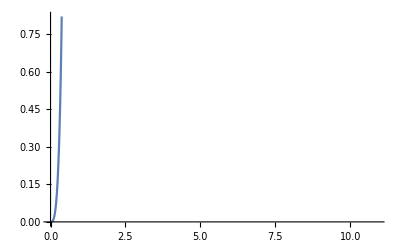

```mathematica
sol2=DSolve[{v'[t]==-u*Log[((M1-M0*t)/M1)]-g*t,v[0]==0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[h2[t],{t,0,10.91}]
```

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

k=ρ2*A2/2
C=0.1
A2=((.06)^2)*Pi

Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

DSolve[{v'[t]==9.81-5.29381 C k v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0})

0.00689894

0.1

0.0113097

-Graphics-

-Graphics-

-Graphics-

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2]},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
```

NDSolve[{V'[t]==0.0130371 pi √(-100000+2 P0 (V0/V[t])^9.81)},V[t],{t,0,1}]

340000.

0

1000

9.81

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2]},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
```

NDSolve[{V'[t]==0.375506 pi √((V0/V[t])^9.81)},V[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2]},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==0.00184838 √((V0/V[t])^9.81)},V[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

0.0015

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2]},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==2.60327×10^-17 √((1/V[t])^9.81)},V[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

0.0015

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2],V[0]==0},v[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==2.60327×10^-17 √((1/V[t])^9.81),V[0]==0},v[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2],V[0]==0},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
0.0015
```

NDSolve[{V'[t]==2.60327×10^-17 √((1/V[t])^9.81),V[0]==0},V[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

0.0015

0.0015

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2],V[0]==0},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve::deqn: Equation or list of equations expected instead of False in the first argument {V'[t]==0.0000708822 √((-P2+2 Power[«2»] P0 Power[«2»])/ρ2),False}.

NDSolve[{V'[t]==0.0000708822 √((-P2+2 0.0015^g P0 (1/V[t])^g)/ρ2),False},V[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

0.0015

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2],V[0]==0},V[t],{t,1,4}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==2.60327×10^-17 √((1/V[t])^9.81),V[0]==0},V[t],{t,1,4}]

340000.

0

1000

9.81

0.0000708822

0.0015

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(gamma)-P2)/ρ2],V[0]==0},V[t],{t,0,4}]
P0=3.4*10^5
P2=0
ρ2=1000
gamma=5/7
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==0.00184838 √(0.0015^gamma (1/V[t])^gamma),V[0]==0},V[t],{t,0,4}]

340000.

0

1000

5/7

0.0000708822

0.0015

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g1)-P2)/ρ2],V[0]==0},V[t],{t,0,4}]
P0=3.4*10^5
P2=0
ρ2=1000
g1=5/7
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==0.00184838 √(0.0015^g1 (1/V[t])^g1),V[0]==0},V[t],{t,0,4}]

340000.

0

1000

5/7

0.0000708822

0.0015

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g1)-P2)/ρ2],V[0]==0},V[t],{t,0,4}]
P0=3.4*10^5
P2=0
ρ2=1000
g1=5/7
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==0.000181239 (1/V[t])^(5/14),V[0]==0},V[t],{t,0,4}]

340000.

0

1000

5/7

0.0000708822

0.0015

```mathematica
ClearAll
```

ClearAll

```mathematica
sol2=DSolve[{v'[t]==(2*A(P1-P2))/(M-ρ1*ve*A*t),v[0]==0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

P1=3.4*10^5
P2=0
ve=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81
ρ1=1000
A=((4.75*10^(-3))^2)*Pi
```

{{v[t]→(680. (1. Log[1. M]-1. Log[1. M-0.0708822 t ve]))/ve}}

(680. (1. Log[1. M]-1. Log[1. M-0.0708822 t ve]))/ve

(680. t)/ve+(680. t Log[M])/ve+(9593.38 M Log[1. M-0.0708822 t ve])/ve^2-(680. t Log[1. M-0.0708822 t ve])/ve

48.1999/(1. M-0.0708822 t ve)

340000.

0

26.0768

0.1889

0.6889

1.84838

9.81

1000

0.0000708822

```mathematica
Plot[h2[t],{t,0,10.91}]
Plot[vsol2[t],{t,0,10.91}]
Plot[a2[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ClearAll
```

ClearAll

{{v[t]→-(9.81 (1. t ve ρ1-69317. Log[M0]+0.203874 P2 Log[M0]+69317. Log[M0-1. A t ve ρ1]-0.203874 P2 Log[M0-1. A t ve ρ1]))/(ve ρ1)}}

-(9.81 (1. t ve ρ1-69317. Log[M0]+0.203874 P2 Log[M0]+69317. Log[M0-1. A t ve ρ1]-0.203874 P2 Log[M0-1. A t ve ρ1]))/(ve ρ1)

-4.905 t^2+(680000. t)/(ve ρ1)-(2. P2 t)/(ve ρ1)+(680000. t Log[M0])/(ve ρ1)-(2. P2 t Log[M0])/(ve ρ1)+(680000. M0 Log[M0-1. A t ve ρ1])/(A ve^2 ρ1^2)-(2. M0 P2 Log[M0-1. A t ve ρ1])/(A ve^2 ρ1^2)-(680000. t Log[M0-1. A t ve ρ1])/(ve ρ1)+(2. P2 t Log[M0-1. A t ve ρ1])/(ve ρ1)

-(9.81 (1. ve ρ1-(69317. A ve ρ1)/(M0-1. A t ve ρ1)+(0.203874 A P2 ve ρ1)/(M0-1. A t ve ρ1)))/(ve ρ1)

340000.

0

26.0768

0.1889

0.6889

1.84838

9.81

1000

0.0000708822

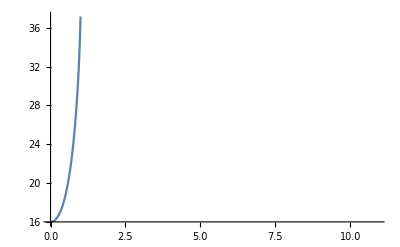

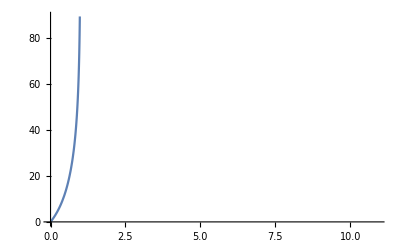

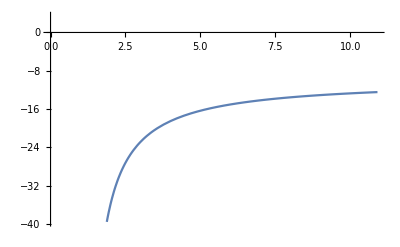

```mathematica
sol2=DSolve[{v'[t]==(2*A(P1-P2))/(M0-ρ1*ve*A*t)-g,v[0]==0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

P1=3.4*10^5
P2=0
ve=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81
ρ1=1000
A=((4.75*10^(-3))^2)*Pi

Plot[h2[t],{t,0,10.91}]
Plot[vsol2[t],{t,0,10.91}]
Plot[a2[t],{t,0,10.91}]
```

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
ve=26.07680962
```

DSolve[{v'[t]==9.81-0.0365216 C v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
v=26.07680962
```

DSolve[{v'[t]==9.81-0.0365216 C v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
ClearAll
```

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
v=26.07680962
```

DSolve[{0==9.81-24.8347 C,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

```mathematica
ClearAll
```

ClearAll

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v1^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
v1=26.07680962
```

DSolve[{0==9.81-0.0365216 C v1^2,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-0.0365216 C v1^2,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-0.0365216 C v1^2,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-0.0365216 C v1^2,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
ClearAll
```

ClearAll

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
ve=26.07680962
```

DSolve[{0==9.81-24.8347 C,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
sol3=DSolve[{v'[t]==g-(k*(C)*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
ve=26.07680962
```

DSolve[{0==9.81-24.8347 C,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
sol3=DSolve[{v'[t]==g-(k*(C)*(ve)^(2))/(M_2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M_2=.1889
ve=26.07680962
```

DSolve[{0==9.81-(2.34564 C)/M_,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-(2.34564 C)/M_,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-(2.34564 C)/M_,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-(2.34564 C)/M_,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
ClearAll
```

ClearAll

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.5
M2=.1889
ve=26.07680962

Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

DSolve[{0==9.81-24.8347 C,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.5

0.1889

```mathematica
C
```

C

```mathematica
C
```

C

```mathematica
C = 0.1
```

0.1

```mathematica
C
```

C

```mathematica
sol3=DSolve[{v'[t]==g-(k*x*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
x=0.5
M2=.1889
ve=26.07680962

Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

DSolve[{0==9.81-24.8347 x,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-24.8347 x,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-24.8347 x,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-24.8347 x,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.5

0.1889

26.0768

-Graphics-

-Graphics-

-Graphics-

```mathematica
C =
```

```mathematica
ve
```

26.0768

```mathematica
x
```

0.5

```mathematica
sol3=DSolve[{v'[t]==g-(k*x*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

DSolve[{False,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{False,26.0768[0]==0}

∫(26.0768[t]/.{False,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{False,26.0768[0]==0})

```mathematica
ClearAll
```

ClearAll

```mathematica
ve
```

26.0768

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ve
```

26.0768

```mathematica
v
```

26.0768

```mathematica
Clear["Global`*"]
```

```mathematica
v
```

v

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

g=9.8
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.5
M2=.1889
ve=26.07680962
```

{{v[t]→(g M2 t-C k t ve^2)/M2}}

(g M2 t-C k t ve^2)/M2

1/2 t^2 (g-(C k ve^2)/M2)

(g M2-C k ve^2)/M2

9.8

1.22

0.0113097

0.00689894

0.5

0.1889

26.0768

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

{{v[t]→9.8 t-24.8347 C t}}

9.8 t-24.8347 C t

4.9 t^2-12.4174 C t^2

9.8-24.8347 C

```mathematica
c
```

c

```mathematica
C
```

C

```mathematica
C = 0.1
```

0.1

```mathematica
C
```

C

```mathematica
c = 1
```

1

```mathematica
c
```

1

```mathematica
c = .1
```

0.1

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

{{v[t]→7.31653 t}}

7.31653 t

3.65826 t^2

7.31653

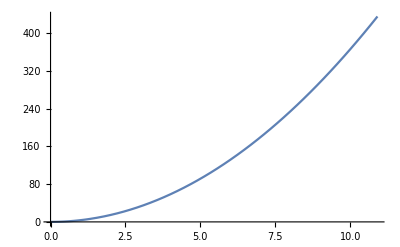

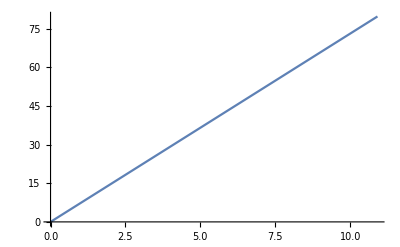

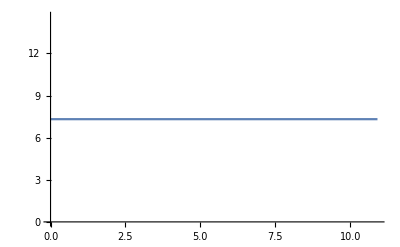

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

```mathematica
sol3=DSolve[{v'[t]==(k*c*(ve)^(2))/(M2)-g,v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

{{v[t]→-7.31653 t}}

-7.31653 t

-3.65826 t^2

-7.31653

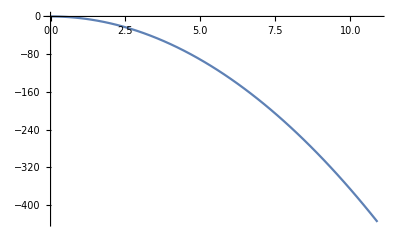

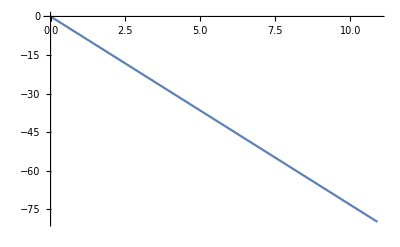

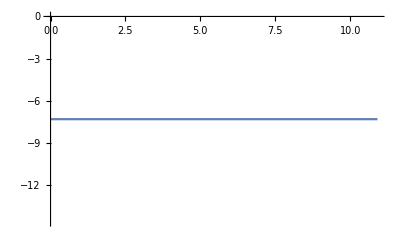

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

```mathematica
sol4=DSolve[{v'[t]==g+(k*c*v^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]
```

DSolve[{v'[t]==9.8+0.00365216 v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.8+0.00365216 v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.8+0.00365216 v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.8+0.00365216 v^2,v[0]==0})

```mathematica
sol4=DSolve[{v'[t]==g+(k*c*(ve)^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]
```

{{v[t]→12.2835 t}}

12.2835 t

6.14174 t^2

12.2835

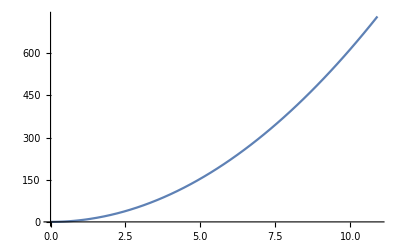

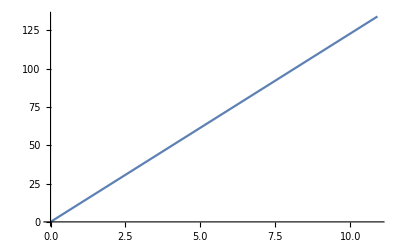

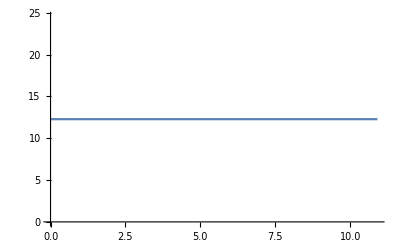

```mathematica
Plot[h4[t],{t,0,10.91}]
Plot[vsol4[t],{t,0,10.91}]
Plot[a4[t],{t,0,10.91}]
```

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(v)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

g=9.81
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.5
M2=.1889
ve=26.07680962
```

DSolve[{v'[t]==9.8-0.00365216 v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.8-0.00365216 v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.8-0.00365216 v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.8-0.00365216 v^2,v[0]==0})

9.81

1.22

```mathematica
Clear
```

0.0113097

0.00689894

0.5

0.1889

26.0768

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Clear["Global`*"]
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M1-g,v[0]==0},v[t],t]
vsol1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[vsol1[t],t]
a1[t_]=D[vsol1[t],t]

P1=3.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M1=0.6889
g=9.81
```

{{v[t]→(-g M1 t+A1 P1 t)/M1}}

(-g M1 t+A1 P1 t)/M1

-(g t^2)/2+(A1 P1 t^2)/(2 M1)

(-g M1+A1 P1)/M1

340000.

0.0000708822

0.6889

9.81

```mathematica
Clear[g,k,c,M2]
sol3=DSolve[{v'[t]==g-(k*c*(v[t])^(2))/(M2),v[0]== v0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]


g=9.81
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.1
M2=.1889
v0=30
ve=26.07680962


Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(√g √M2 Tanh[(√c √g √k t+√M2 ArcTanh[(√c √k v0)/(√g √M2)])/(√M2)])/(√c √k)}}

(√g √M2 Tanh[(√c √g √k t+√M2 ArcTanh[(√c √k v0)/(√g √M2)])/(√M2)])/(√c √k)

```mathematica
h3[t]
```

54.7621 Log[Cos[0.423248 t-ArcTan[0.0431445 v0]]]

9.81

1.22

0.0113097

0.00689894

0.5

0.1889

26.0768

```mathematica
sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(23.1779 (-1.+1. ⅇ^(0.846495 t)))/(1.+1. ⅇ^(0.846495 t))}}

-(23.1779 (-1.+1. ⅇ^(0.846495 t)))/(1.+1. ⅇ^(0.846495 t))

23.1779 t-54.7621 Log[1.+ⅇ^(0.846495 t)]

```mathematica
(19.620000000000005 ⅇ^(0.84649544751168 t) (-1.+1. ⅇ^(0.84649544751168 t)))/((1.+1. ⅇ^(0.84649544751168 t))^2)-(19.620000000000005 ⅇ^(0.84649544751168 t))/(1.+1. ⅇ^(0.84649544751168 t))
Clear[g,k,c,M2]
```

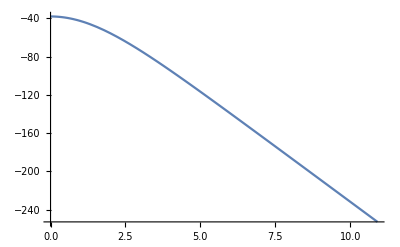

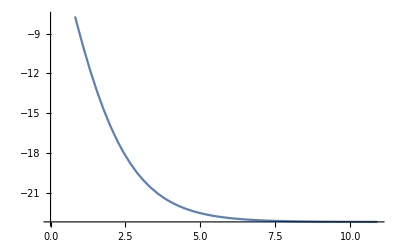

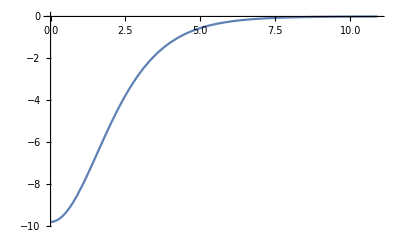

```mathematica
Plot[h4[t],{t,0,10.91}]
Plot[vsol4[t],{t,0,10.91}]
Plot[a4[t],{t,0,10.91}]
```

```mathematica
sol4=DSolve[{v'[t]==g-(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))}}

(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))

-51.8274 t+273.81 Log[1.+ⅇ^(0.378564 t)]

-(19.62 ⅇ^(0.378564 t) (-1.+1. ⅇ^(0.378564 t)))/((1.+1. ⅇ^(0.378564 t))^2)+(19.62 ⅇ^(0.378564 t))/(1.+1. ⅇ^(0.378564 t))

```mathematica
g=9.81
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.1
M2=.1889
ve=26.07680962
```

9.81

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
c
```

0.12

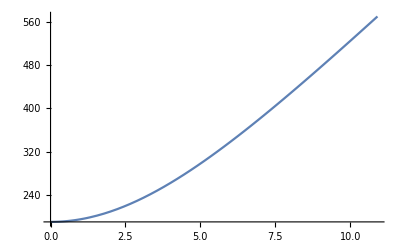

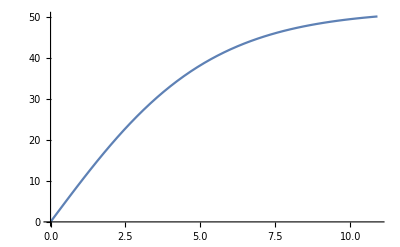

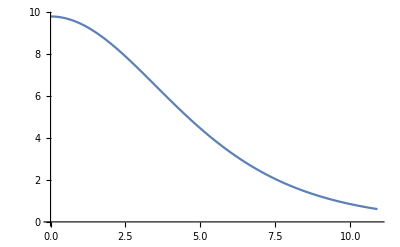

```mathematica
Plot[h4[t],{t,0,10.91}]
Plot[vsol4[t],{t,0,10.91}]
Plot[a4[t],{t,0,10.91}]
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M1-g,v[0]==0},v[t],t]
vsol1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[vsol1[t],t]
a1[t_]=D[vsol1[t],t]
```

{{v[t]→(-g M1 t+A1 P1 t)/M1}}

(-g M1 t+A1 P1 t)/M1

-(g t^2)/2+(A1 P1 t^2)/(2 M1)

(-g M1+A1 P1)/M1

```mathematica
sol2=DSolve[{v'[t]==(2*A(P1-P2))/(M0-ρ1*ve*A*t)-g,v[0]==vsol1[t1]},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]
```

{{v[t]→-245.201-9.81 t-26.0768 Log[0.0000708822-1. A t]}}

-245.201-9.81 t-26.0768 Log[0.0000708822-1. A t]

-219.124 t-4.905 t^2+(0.00184838 Log[0.0000708822-1. A t])/A-26.0768 t Log[0.0000708822-1. A t]

-9.81+(26.0768 A)/(0.0000708822-1. A t)

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(v[t])^(2))/(M2),v[0]==vsol2[t2]},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(51.8274 (1. ⅇ^(0.378564 t)-1. ((-4.79373×10^15-4.17126×10^14 Log[0.0000708822-0.270507 A])/(3.13566×10^15+4.17126×10^14 Log[0.0000708822-0.270507 A]))^1.))/(1. ⅇ^(0.378564 t)+1. ((-4.79373×10^15-4.17126×10^14 Log[0.0000708822-0.270507 A])/(3.13566×10^15+4.17126×10^14 Log[0.0000708822-0.270507 A]))^1.)}}

(51.8274 (1. ⅇ^(0.378564 t)-1. ((-4.79373×10^15-4.17126×10^14 Log[0.0000708822-0.270507 A])/(3.13566×10^15+4.17126×10^14 Log[0.0000708822-0.270507 A]))^1.))/(1. ⅇ^(0.378564 t)+1. ((-4.79373×10^15-4.17126×10^14 Log[0.0000708822-0.270507 A])/(3.13566×10^15+4.17126×10^14 Log[0.0000708822-0.270507 A]))^1.)

(t (-2.20181×10^17-2.16186×10^16 Log[0.000262035-1. A])+(2.64156 (1.14067×10^33+2.95683×10^32 Log[0.000262035-1. A]+1.80353×10^31 Log[0.000262035-1. A]^2) Log[4.24836×10^15-2.59029×10^15 ⅇ^(0.378564 t)+(4.17126×10^14-4.17126×10^14 ⅇ^(0.378564 t)) Log[0.000262035-1. A]])/(2.59029×10^15+4.17126×10^14 Log[0.000262035-1. A]))/(4.24836×10^15+4.17126×10^14 Log[0.000262035-1. A])

-(19.62 ⅇ^(0.378564 t) (1. ⅇ^(0.378564 t)-1. ((-4.79373×10^15-4.17126×10^14 Log[0.0000708822-0.270507 A])/(3.13566×10^15+4.17126×10^14 Log[0.0000708822-0.270507 A]))^1.))/((1. ⅇ^(0.378564 t)+1. ((-4.79373×10^15-4.17126×10^14 Log[0.0000708822-0.270507 A])/(3.13566×10^15+4.17126×10^14 Log[0.0000708822-0.270507 A]))^1.)^2)+(19.62 ⅇ^(0.378564 t))/(1. ⅇ^(0.378564 t)+1. ((-4.79373×10^15-4.17126×10^14 Log[0.0000708822-0.270507 A])/(3.13566×10^15+4.17126×10^14 Log[0.0000708822-0.270507 A]))^1.)

```mathematica
sol4=DSolve[{v'[t]==g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→18.3238 Tan[0.535371 t]}}

18.3238 Tan[0.535371 t]

-34.2263 Log[Cos[0.535371 t]]

9.81 Sec[0.535371 t]^2

```mathematica
P1=4.4*10^5
P2=10^5
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
M0=1.8483812
M1=0.6889
M2=.1889
g=9.81
ρ1=1000
ρ2=1.22
k=ρ2*A2/2
```

440000.

100000

0.0000708822

0.0113097

1.84838

0.6889

0.1889

9.81

1000

1.22

0.00689894

```mathematica
c=0.1

v0=30
ve=26.07680962
t1=0.1113732799
t2=0.2705069712
t3=vsol2[t2]
t4=10.91
```

0.1

30

26.0768

0.111373

0.270507

0.0000556659 (311055.-468452. Log[1.84838-7053.96 A])

10.91

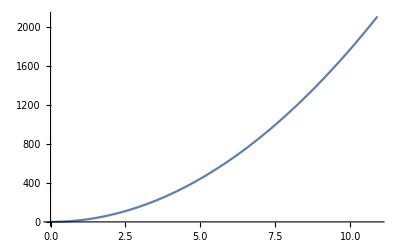

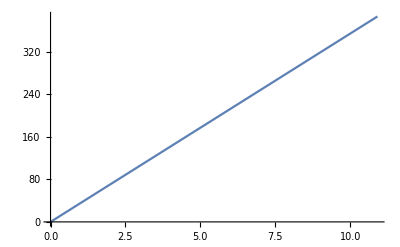

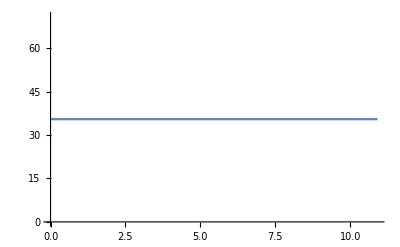

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

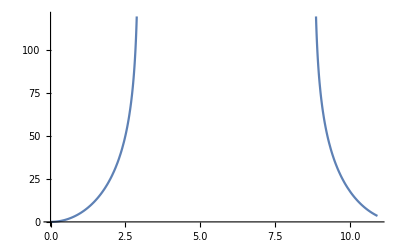

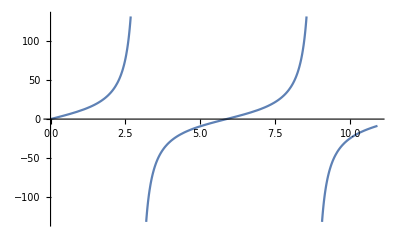

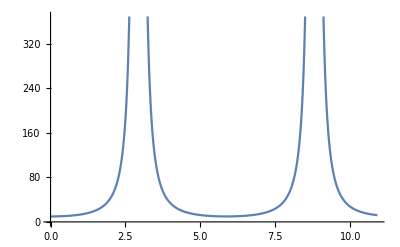

```mathematica
Plot[h1[t],{t,0,10.91}]
Plot[vsol1[t],{t,0,10.91}]
Plot[a1[t],{t,0,10.91}]

Plot[h2[t],{t,0,10.91}]
Plot[vsol2[t],{t,0,10.91}]
Plot[a2[t],{t,0,10.91}]

Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]

Plot[h4[t],{t,0,10.91}]
Plot[vsol4[t],{t,0,10.91}]
Plot[a4[t],{t,0,10.91}]
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M1-g,v[0]==0},v[t],t]
vsol1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[vsol1[t],t]
a1[t_]=D[vsol1[t],t]
```

{{v[t]→(-g M1 t+A1 P1 t)/M1}}

(-g M1 t+A1 P1 t)/M1

-(g t^2)/2+(A1 P1 t^2)/(2 M1)

(-g M1+A1 P1)/M1

```mathematica
P1=4.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M1=0.6889
g=9.81

Plot[h1[t],{t,0,10.91}]
Plot[vsol1[t],{t,0,10.91}]
Plot[a1[t],{t,0,10.91}]
```

440000.

0.0000708822

0.6889

9.81

-Graphics-

-Graphics-

-Graphics-

```mathematica
t1 =Solve[h1[t] == .22, t]
```

{{t→-0.111389},{t→0.111389}}

```mathematica
vsol1[t1]
t
```

{{35.4624 (t→-0.111389)},{35.4624 (t→0.111389)}}

```mathematica
t
Clear[t]
```

t

```mathematica
P1=4.4*10^5
P2=10^5
ve=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81
ρ1=1000
A=((4.75*10^(-3))^2)*Pi
```

440000.

100000

26.0768

0.1889

0.6889

1.84838

```mathematica
sol2=DSolve[{v'[t]==(2*A(P1-P2))/(M0-ρ1*ve*A*t)-g,v[0]==35.46240683482751},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]
```

{{v[t]→35.4624-9.81 t-26.0768 Log[1.-1. t]}}

35.4624-9.81 t-26.0768 Log[1.-1. t]

61.5392 t-4.905 t^2+26.0768 Log[1.-1. t]-26.0768 t Log[1.-1. t]

-9.81+26.0768/(1.-1. t)

```mathematica
P1=4.4*10^5
P2=10^5
ve=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81
ρ1=1000
A=((4.75*10^(-3))^2)*Pi
```

440000.

100000

26.0768

0.1889

0.6889

1.84838

9.81

1000

0.0000708822

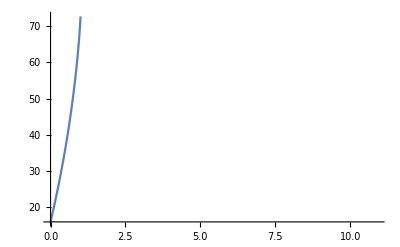

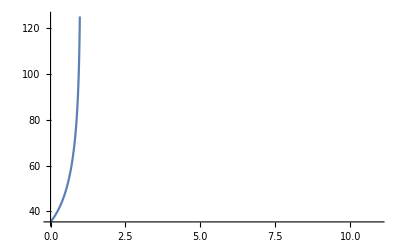

-Graphics-

```mathematica
Plot[h2[t],{t,0,10.91}]
Plot[vsol2[t],{t,0,10.91}]
Plot[a2[t],{t,0,10.91}]
```

```mathematica
vsol2[.27]
```

41.0204

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(v[t])^(2))/(M2),v[0]=v0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

DSolve::deqn: Equation or list of equations expected instead of v0 in the first argument {v'[t]==g-(c k v[t]^2)/M2,v0}.

DSolve[{v'[t]==g-(c k v[t]^2)/M2,v0},v[t],t]

ReplaceAll::reps: {v'[t]==g-(c k v[t]^2)/M2,v0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v[t]/.{v'[t]==g-(c k v[t]^2)/M2,v0}

ReplaceAll::reps: {v'[t]==g-(c k v[t]^2)/M2,v0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {g==(c k (Integrate`Y)^2)/M2+v'[t],v0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

∫(v[t]/.{v'[t]==g-(c k v[t]^2)/M2,v0})ⅆt

ReplaceAll::reps: {v'[t]==g-(c k v[t]^2)/M2,v0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∂_t (v[t]/.{v'[t]==g-(c k v[t]^2)/M2,v0})

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(v[t])^(2))/(M2),v[0]==v0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {v'[t]==g-(c k v[t]^2)/M2,True}.

DSolve[{v'[t]==g-(c k v[t]^2)/M2,True},v[t],t]

ReplaceAll::reps: {v'[t]==g-(c k v[t]^2)/M2,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v[t]/.{v'[t]==g-(c k v[t]^2)/M2,True}

ReplaceAll::reps: {v'[t]==g-(c k v[t]^2)/M2,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {g==(c k (Integrate`Y)^2)/M2+v'[t],True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

∫(v[t]/.{v'[t]==g-(c k v[t]^2)/M2,True})ⅆt

ReplaceAll::reps: {v'[t]==g-(c k v[t]^2)/M2,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∂_t (v[t]/.{v'[t]==g-(c k v[t]^2)/M2,True})

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(v[t])^(2))/(M2),v[0]==v0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(√g √M2 Tanh[(√c √g √k t+√M2 ArcTanh[(√c √k v0)/(√g √M2)])/(√M2)])/(√c √k)}}

(√g √M2 Tanh[(√c √g √k t+√M2 ArcTanh[(√c √k v0)/(√g √M2)])/(√M2)])/(√c √k)

```mathematica
g=9.81
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
v0=41.0204
M2=.1889
ve=26.07680962
```

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k v0)/(√g √M2)])/(√M2)])/(√c √k)}}

(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k v0)/(√g √M2)])/(√M2)])/(√c √k)

(M2 Log[Cos[(√c √g √k t)/(√M2)-ArcTan[(√c √k v0)/(√g √M2)]]])/(c k)

-g Sec[(-√c √g √k t+√M2 ArcTan[(√c √k v0)/(√g √M2)])/(√M2)]^2

9.81

1.22

0.0113097

0.00689894

0.8

41.0204

0.1889

26.0768

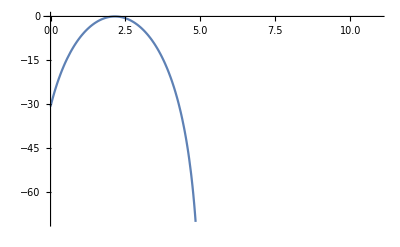

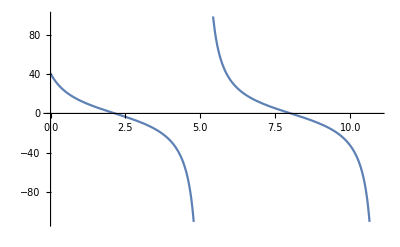

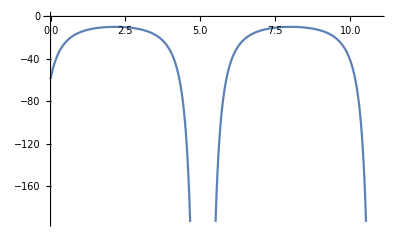

```mathematica
Clear[g,k,c,v0]
sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==v0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

g=9.81
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
v0=41.0204
M2=.1889
ve=26.07680962

Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(v[t])^(2))/(M2),v[0]==v0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(v[t])^(2))/(M2),v[0]==v0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
tsol3 = Solve[h3[t]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→1684.05 √M2 Tanh[(1.75968×10^-13 (3.31039×10^10 t+5.68285×10^12 √M2 ArcTanh[(0.000593805 v0)/(√M2)]))/(√M2)]}}

1684.05 √M2 Tanh[(1.75968×10^-13 (3.31039×10^10 t+5.68285×10^12 √M2 ArcTanh[(0.000593805 v0)/(√M2)]))/(√M2)]

289097. M2 Log[Cosh[(0.00582523 t)/(√M2)+1. ArcTanh[(0.000593805 v0)/(√M2)]]]

9.81 Sech[(1.75968×10^-13 (3.31039×10^10 t+5.68285×10^12 √M2 ArcTanh[(0.000593805 v0)/(√M2)]))/(√M2)]^2

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.-171.667 √M2 ArcTanh[(0.000593805 v0)/(√M2)]}}

```mathematica
sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))}}

-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))

18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]

(19.62 ⅇ^(1.07074 t) (-1.+1. ⅇ^(1.07074 t)))/((1.+1. ⅇ^(1.07074 t))^2)-(19.62 ⅇ^(1.07074 t))/(1.+1. ⅇ^(1.07074 t))

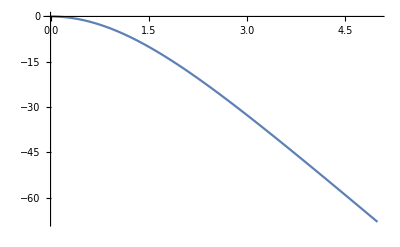

```mathematica
Plot[h4[t]-h4[0],{t,0,5}]
```

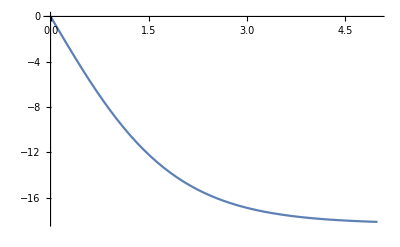

```mathematica
Plot[vsol4[t],{t,0,5}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))}}

-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))

18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]

(19.62 ⅇ^(1.07074 t) (-1.+1. ⅇ^(1.07074 t)))/((1.+1. ⅇ^(1.07074 t))^2)-(19.62 ⅇ^(1.07074 t))/(1.+1. ⅇ^(1.07074 t))

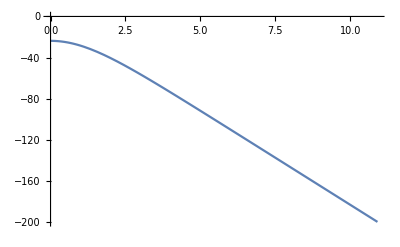

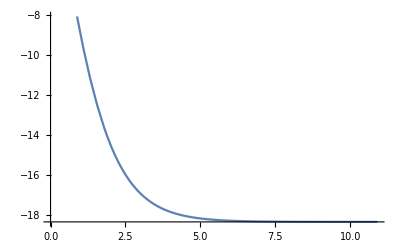

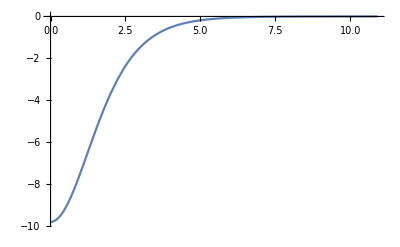

```mathematica
Plot[a4[t],{t,0,10.91}]
```

```mathematica
g Sec[(√c √g √k t)/(√M2)]^2
g=9.81
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
v0=41.0204
M2=.1889
ve=26.07680962
```

g Sec[(√c √g √k t)/(√M2)]^2

9.81

1.22

0.0113097

0.00689894

0.8

41.0204

0.1889

26.0768

```mathematica
Plot[h4[t],{t,0,10.91}]
Plot[vsol4[t],{t,0,10.91}]
Plot[a4[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
t1=0.111389
t2=0.2705069712
t3=
```

0.111389

0.270507

```mathematica
vcom[t_]:=vsol1[t]/;t<t1
```

```mathematica
vcom[t_]:=vsol2[t]/;t1<t<t2
```

```mathematica
vcom[t_]:=vsol3[t]/;t2<t<t3
```

```mathematica
vcom[t_]:=vsol4[t]/;t3<t<t4
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M1-g,v[0]==0},v[t],t]
vsol1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[vsol1[t],t]
a1[t_]=D[vsol1[t],t]
```

{{v[t]→(100000. (1. A1 t-0.0000981 M1 t))/M1}}

(100000. (1. A1 t-0.0000981 M1 t))/M1

1/2 (-9.81+(100000. A1)/M1) t^2

(100000. (1. A1-0.0000981 M1))/M1

```mathematica
Clear[L] 
Clear[v0]
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M1-g,v[0]==0},v[t],t]
vsol1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[vsol1[t],t]
a1[t_]=D[vsol1[t],t]
```

{{v[t]→-(9.81 (-3.17922 t+1. M1 t))/M1}}

-(9.81 (-3.17922 t+1. M1 t))/M1

((31.1882-9.81 M1) t^2)/(2 M1)

-(9.81 (-3.17922+1. M1))/M1

```mathematica
tsol1 = Solve[h1[t]== L,t]
v0 = Simplify[vsol1[t]/.tsol1[[2]]]
```

{{t→-0.111389},{t→0.111389}}

3.95012

```mathematica
P1=4.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M1=0.6889
g=9.81
L=.22
```

440000.

0.0000708822

0.6889

9.81

0.22

```mathematica
Plot[h1[t],{t,0,10.91}]

Plot[vsol1[t],{t,0,10.91}]

Plot[a1[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

{{t→-0.111389},{t→0.111389}}

0.111389

```mathematica
vsol1[t]
```

35.4624 t

```mathematica
Clear[vsol1,tsol1]
```

```mathematica
vsol1
```

```mathematica
vsol1
v0
```

vsol1

8.42169 √L

```mathematica
sol2=DSolve[{v'[t]==(2*A(P1-P2))/(M0-ρ1*ve*A*t)-g,v[0]==v0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]
```

{{v[t]→-270.938-9.81 t-26.0768 Log[0.0000264181-1. A t]}}

-270.938-9.81 t-26.0768 Log[0.0000264181-1. A t]

-244.861 t-4.905 t^2+(0.0006889 Log[0.0000264181-1. A t])/A-26.0768 t Log[0.0000264181-1. A t]

-9.81+(26.0768 A)/(0.0000264181-1. A t)

```mathematica
M[t_]=M0-A*ve*1000*t
```

0.6889-26076.8 A t

```mathematica
M[t]==M0-1.848381224048865 t

tsol2=Solve[M[t]==0,t]
v1=Simplify[vsol2[t]/.tsol2[[1]]]
```

0.6889-26076.8 A t==0.6889-1.84838 t

{{t→0.0000264181/A}}

Indeterminate

```mathematica
Clear[M0]
```

```mathematica
P1=4.4*10^5
P2=10^5
ve=26.07680962
M0=.1889
M1=.6889
g=9.81
ρ1=1000
A=((4.75*10^(-3))^2)*Pi
L=.22
```

```mathematica
v1
```

Indeterminate

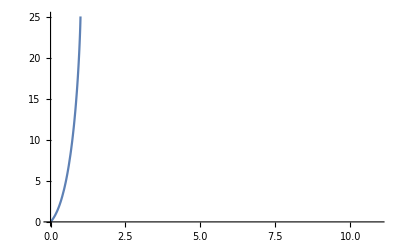

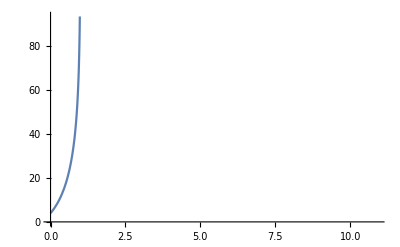

-Graphics-

```mathematica
Plot[h2[t],{t,0,10.91}]

Plot[vsol2[t],{t,0,10.91}]

Plot[a2[t],{t,0,10.91}]
```

```mathematica
M[t]==M0-A*ve*1000*t
```

M[t]==1.84838-1.84838 t

```mathematica
sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==v0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→2381.61 √M2 Tan[(8.7984×10^-14 (-4.6816×10^10 t+1.13657×10^13 √M2 ArcTan[(0.000419884 v0)/(√M2)]))/(√M2)]}}

2381.61 √M2 Tan[(8.7984×10^-14 (-4.6816×10^10 t+1.13657×10^13 √M2 ArcTan[(0.000419884 v0)/(√M2)]))/(√M2)]

578193. M2 Log[Cos[(0.00411906 t)/(√M2)-1. ArcTan[(0.000419884 v0)/(√M2)]]]

-9.81 Sec[(8.7984×10^-14 (-4.6816×10^10 t+1.13657×10^13 √M2 ArcTan[(0.000419884 v0)/(√M2)]))/(√M2)]^2

```mathematica
tsol3=Solve[vsol3[t]==0,t]
v2=Simplify[vsol3[t]/.tsol3[[2]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.+242.774 √M2 ArcTan[(0.000419884 v0)/(√M2)]}}

Part::partw: Part 2 of {{t→0.+242.774 √M2 ArcTan[0.000419884 Power[«2»] v0]}} does not exist.

ReplaceAll::reps: {{{t→0.+242.774 Power[«2»] ArcTan[«1»]}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-2381.61 √M2 Tan[(0.00411906 t)/(√M2)-1. ArcTan[(0.000419884 v0)/(√M2)]]/.{{t→242.774 √M2 ArcTan[(0.000419884 v0)/(√M2)]}}⟦2⟧

```mathematica
g=9.81
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
v0=41.0204
M2=.1889
ve=26.07680962
```

9.81

1.22

0.0113097

0.00689894

0.8

41.0204

0.1889

26.0768

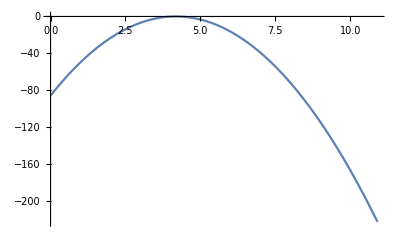

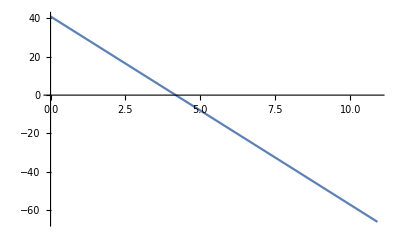

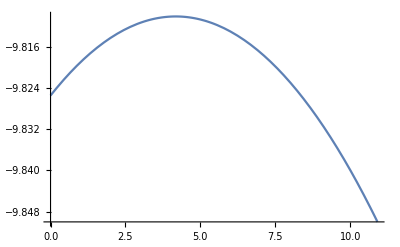

```mathematica
Plot[h3[t],{t,0,10.91}]

Plot[vsol3[t],{t,0,10.91}]

Plot[a3[t],{t,0,10.91}]
```

```mathematica
sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))}}

-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))

18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]

(19.62 ⅇ^(1.07074 t) (-1.+1. ⅇ^(1.07074 t)))/((1.+1. ⅇ^(1.07074 t))^2)-(19.62 ⅇ^(1.07074 t))/(1.+1. ⅇ^(1.07074 t))

```mathematica
tsol4=Solve[h4[t]==0,t]
v3=Simplify[vsol4[t]/.tsol4[[2]]]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]==0,t]

ReplaceAll::reps: {t} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(18.3238-18.3238 ⅇ^(1.07074 t))/(1.+1. ⅇ^(1.07074 t))/.t

```mathematica
g=9.81
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
v0=41.0204
M2=.1889
ve=26.07680962
```

9.81

1.22

0.0113097

0.00689894

0.8

41.0204

0.1889

26.0768

```mathematica
Plot[h4[t]-h4[0],{t,0,5}]

Plot[vsol4[t],{t,0,10.91}]

Plot[a4[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
vsol1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[vsol1[t],t]
a1[t_]=D[vsol1[t],t]
```

{{v[t]→35.4624 t}}

35.4624 t

17.7312 t^2

35.4624

```mathematica
tsol1=Solve[h1[t]==L,t]
v0=Simplify[vsol1[t]/.tsol1[[2]]]
```

{{t→-0.111389},{t→0.111389}}

3.95012

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
P1=4.4*10^5
M0=0.6889
```

0.22

0.0000708822

440000.

0.6889

```mathematica
sol2=DSolve[{v'[t]==(2*A1(P1-P2))/(M0-ρ1*ve*A1*t)-g,v[0]==v0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]
```

{{v[t]→-21.7869-9.81 t-26.0768 Log[0.372705-1. t]}}

-21.7869-9.81 t-26.0768 Log[0.372705-1. t]

4.28992 t-4.905 t^2+9.71894 Log[0.372705-1. t]-26.0768 t Log[0.372705-1. t]

-9.81+26.0768/(0.372705-1. t)

```mathematica
(0.66332495807108 (-1.507556722888818 g ve ρ1+(1.3266499161421598*^6 ve ρ1)/(9718.9442921668-1. t ve ρ1)-(3.015113445777636 P2 ve ρ1)/(9718.9442921668-1. t ve ρ1)))/(ve ρ1)
Clear[A1,M0]
```

(0.663325 (-1.50756 g ve ρ1+(1.32665×10^6 ve ρ1)/(9718.94-1. t ve ρ1)-(3.01511 P2 ve ρ1)/(9718.94-1. t ve ρ1)))/(ve ρ1)

```mathematica
M[t_]=M0-A1*ve*1000*t
```

0.6889-1.84838 t

```mathematica
tsol2=Solve[M[t]==0,t]
```

{{t→0.372705}}

```mathematica
v1=Simplify[vsol2[t]/.tsol2[[1]]]
```

{{t→0.372705}}

Indeterminate

```mathematica
A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
ve=26.07680962
```

0.0000708822

0.6889

26.0768

1000

ClearAll

```mathematica
sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==v1},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

{}

v[t]/.{}⟦1⟧

∫(v[t]/.{}⟦1⟧)ⅆt

∂_t (v[t]/.{}⟦1⟧)

```mathematica
Clear[A1,M0,ve]
```

```mathematica
tsol3=Solve[vsol3[t]==0,t]
v2=Simplify[vsol3[t]/.tsol3[[1]]]
```

{{t→(0.+(√g √M2 ArcTan[(0.663325 √c √(45.2724-1. g) √g √k √M2-0.372705 √c g^(3/2) √k √M2-(33746.5 √c √g √k √M2 Log[1.-0.001 ρ1])/ρ1+(0.0766965 √c √g √k √M2 P2 Log[1.-0.001 ρ1])/ρ1)/(g M2)])/(√c √k))/g}}

0

```mathematica
ρ2=1.22
g=9.81
A2=((.06)^2)*Pi
c=0.8
M2=.1889
k=ρ2*A2/2
```

1.22

9.81

0.0113097

0.8

0.1889

0.00689894

```mathematica
sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]

tsol4=Solve[h4[t]==0,t]
v3=Simplify[h4[t]/.tsol4[[1]]]
```

{{v[t]→-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))}}

-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))

18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]

(19.62 ⅇ^(1.07074 t) (-1.+1. ⅇ^(1.07074 t)))/((1.+1. ⅇ^(1.07074 t))^2)-(19.62 ⅇ^(1.07074 t))/(1.+1. ⅇ^(1.07074 t))

Solve[18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]==0,t]

18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]/.1. t==1.86786 Log[1.+ⅇ^(1.07074 t)]

```mathematica
P1=4.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
M2=.1889
g=9.81
L=.22
P1=4.4*10^5
P2=10^5
ve=26.07680962
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
M2=.1889
ρ1=1000
```

440000.

0.0000708822

0.6889

0.1889

9.81

0.22

440000.

100000

26.0768

1.22

0.0113097

0.00689894

0.8

0.1889

1000

```mathematica
Plot[h1[t],{t,0,10.91}]

Plot[vsol1[t],{t,0,10.91}]

Plot[a1[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

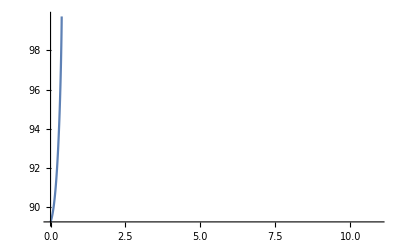

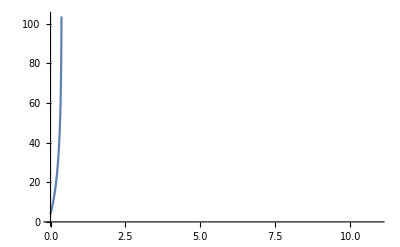

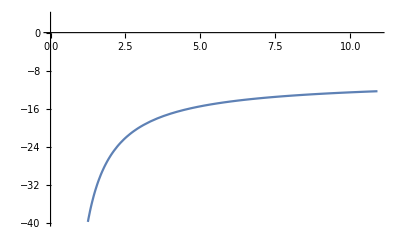

```mathematica
Plot[h2[t],{t,0,10.91}]

Plot[vsol2[t],{t,0,10.91}]

Plot[a2[t],{t,0,10.91}]
```

```mathematica
Plot[h3[t],{t,0,10.91}]

Plot[vsol3[t],{t,0,10.91}]

Plot[a3[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

-(g t^2)/2+(A1 P1 t^2)/(2 M0)

(-g M0+A1 P1)/M0

{{t→-(√2 √L)/(√(-g+(A1 P1)/M0))},{t→(√2 √L)/(√(-g+(A1 P1)/M0))}}

√2 √L √(-g+(A1 P1)/M0)

0.22

0.0000708822

440000.

0.6889

{{v[t]→(0.663325 (1. √(-1. g+(440000. A1)/M0) ve ρ1-1.50756 g t ve ρ1+1.32665×10^6 Log[1. M0]-3.01511 P2 Log[1. M0]-1.32665×10^6 Log[1. M0-1. A1 t ve ρ1]+3.01511 P2 Log[1. M0-1. A1 t ve ρ1]))/(ve ρ1)}}

(0.663325 (1. √(-1. g+(440000. A1)/M0) ve ρ1-1.50756 g t ve ρ1+1.32665×10^6 Log[1. M0]-3.01511 P2 Log[1. M0]-1.32665×10^6 Log[1. M0-1. A1 t ve ρ1]+3.01511 P2 Log[1. M0-1. A1 t ve ρ1]))/(ve ρ1)

((880000.-2. P2) t Log[M0]+(M0 (880000.-2. P2) Log[M0-1. A1 t ve ρ1])/(A1 ve ρ1)+t (880000.-2. P2+0.663325 √(-1. g+(440000. A1)/M0) ve ρ1-0.5 g t ve ρ1+(-880000.+2. P2) Log[1. M0-1. A1 t ve ρ1]))/(ve ρ1)

(0.663325 (-1.50756 g ve ρ1+(1.32665×10^6 A1 ve ρ1)/(1. M0-1. A1 t ve ρ1)-(3.01511 A1 P2 ve ρ1)/(1. M0-1. A1 t ve ρ1)))/(ve ρ1)

M0-1000 A1 t ve

{{t→M0/(1000 A1 ve)}}

Part::partw: Part 2 of {{t→M0/(1000 A1 ve)}} does not exist.

ReplaceAll::reps: {{{t→M0/(1000 A1 ve)}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

((0.663325 √(-1. g+(440000. A1)/M0)-1. g t) ve ρ1+(880000.-2. P2) Log[M0]+(-880000.+2. P2) Log[1. M0-1. A1 t ve ρ1])/(ve ρ1)/.{{t→M0/(1000 A1 ve)}}⟦2⟧

0.0000708822

0.6889

26.0768

Part::partw: Part 2 of {{t→0.372705}} does not exist.

ReplaceAll::reps: {{{t→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k ((0.0383482 (-0.372659 (880000.-2. P2)+26.0768 (0.663325 √(45.2724-1. g)-1. g t) ρ1+(-880000.+2. P2) Log[0.6889-0.00184838 t ρ1]))/ρ1/.{{t→0.372705}}⟦2⟧))/(√g √M2)])/(√M2)])/(√c √k)}}

(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k ((0.0383482 (-0.372659 (880000.-2. P2)+26.0768 (0.663325 √(45.2724-1. g)-1. g t) ρ1+(-880000.+2. P2) Log[0.6889-0.00184838 t ρ1]))/ρ1/.{{t→0.372705}}⟦2⟧))/(√g √M2)])/(√M2)])/(√c √k)

Part::partw: Part 2 of {{t→0.372705}} does not exist.

ReplaceAll::reps: {{{t→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of {{372.705/ρ1-(541.014 Integrate`Y)/ρ1→0.372705}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression #2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

(√g √M2 ∫Tan[(-√c √g √k t+√M2 ArcTan[(√c √k ((0.0383482 (-0.372659 (880000.-2. P2)+26.0768 (0.663325 √(45.2724-1. g)-1. g t) ρ1+(-880000.+2. P2) Log[0.6889-0.00184838 t ρ1]))/ρ1/.{{t→0.372705}}⟦2⟧))/(√g √M2)])/(√M2)]ⅆt)/(√c √k)

Part::partw: Part 2 of {{t→0.372705}} does not exist.

ReplaceAll::reps: {{{t→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1/(√c √k)√g (-√c √g √k+(√c √k ∂_t ((0.0383482 (-0.372659 (880000.-2. P2)+26.0768 (0.663325 √(45.2724-1. g)-1. g t) ρ1+(-880000.+2. P2) Log[0.6889-0.00184838 t ρ1]))/ρ1/.{{t→0.372705}}⟦2⟧))/(√g (1+(c k ((0.0383482 (-0.372659 (880000.-2. P2)+26.0768 (0.663325 √(45.2724-1. g)-1. g t) ρ1+(-880000.+2. P2) Log[0.6889-0.00184838 t ρ1]))/ρ1/.{{t→0.372705}}⟦2⟧)^2)/(g M2)))) Sec[(-√c √g √k t+√M2 ArcTan[(√c √k ((0.0383482 (-0.372659 (880000.-2. P2)+26.0768 (0.663325 √(45.2724-1. g)-1. g t) ρ1+(-880000.+2. P2) Log[0.6889-0.00184838 t ρ1]))/ρ1/.{{t→0.372705}}⟦2⟧))/(√g √M2)])/(√M2)]^2

Part::partw: Part 2 of {{t→0.372705}} does not exist.

ReplaceAll::reps: {{{t→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{System`TSolveDump`X$1739[1]→0.372705}} does not exist.

ReplaceAll::reps: {{{System`TSolveDump`X$1739[1]→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{System`TSolveDump`X$1739[1]→87165262/233872309}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{{System`TSolveDump`X$1739[1]→87165262/233872309}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{}

Part::partw: Part 2 of {{t→0.372705}} does not exist.

ReplaceAll::reps: {{{t→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-(√g √M2 Tan[(√c √g √k t)/(√M2)-ArcTan[(√c √k ((-12575.9+0.0285817 P2+0.663325 √(45.2724-1. g) ρ1-1. g t ρ1+(-33746.5+0.0766965 P2) Log[0.6889-0.00184838 t ρ1])/ρ1/.{{t→0.372705}}⟦2⟧))/(√g √M2)]])/(√c √k)/.{}⟦1⟧

1.22

9.81

0.0113097

0.8

0.1889

0.00689894

ReplaceAll::reps: {{{t→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))}}

-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))

18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]

(19.62 ⅇ^(1.07074 t) (-1.+1. ⅇ^(1.07074 t)))/((1.+1. ⅇ^(1.07074 t))^2)-(19.62 ⅇ^(1.07074 t))/(1.+1. ⅇ^(1.07074 t))

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]==0,t]

ReplaceAll::reps: {t} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]/.t

440000.

0.0000708822

0.6889

0.1889

9.81

0.22

440000.

100000

26.0768

1.22

0.0113097

0.00689894

0.8

0.1889

1000

-Graphics-

Part::partw: Part 2 of {{0.000222876→0.372705}} does not exist.

ReplaceAll::reps: {{{0.000222876→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partw: Part 2 of {{0.222876→0.372705}} does not exist.

ReplaceAll::reps: {{{0.222876→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partw: Part 2 of {{0.445529→0.372705}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{{0.445529→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

-Graphics-

-Graphics-

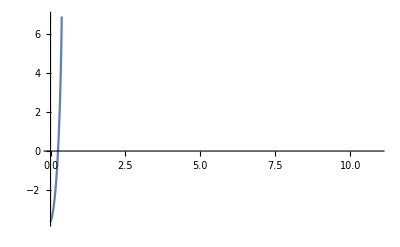

Part::partw: Part 2 of {{0.000222876→0.372705}} does not exist.

ReplaceAll::reps: {{{0.000222876→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partw: Part 2 of {{0.222876→0.372705}} does not exist.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

Part::partw: Part 2 of {{0.445529→0.372705}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

-Graphics-

Part::partw: Part 2 of {{0.000222876→0.372705}} does not exist.

ReplaceAll::reps: {{{0.000222876→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in 0.000222876.

Part::partw: Part 2 of {{0.222876→0.372705}} does not exist.

ReplaceAll::reps: {{{0.222876→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in 0.222876.

-Graphics-

ReplaceAll::reps: {0.000222876} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {0.222876} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {0.445529} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

-Graphics-

Part::partw: Part 2 of {{0.000222876→0.372705}} does not exist.

ReplaceAll::reps: {{{0.000222876→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.000222876 is not a valid variable.

Part::partw: Part 2 of {{0.000222876→0.372705}} does not exist.

ReplaceAll::reps: {{{0.000222876→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{0.000222876→0.372705}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{{0.000222876→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

General::ivar: 0.222876 is not a valid variable.

General::ivar: 0.445529 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[v1[t],t]
a1[t_]=D[v1[t],t]

tsol1=Solve[h1[t]==L,t]
v0=Simplify[v1[t]/.tsol1[[2]]]

L=.22
A1=((4.75*10^(-3))^2)*Pi
P1=4.4*10^5
M0=0.6889

Clear[A1,M0]

sol2=DSolve[{v'[t]==(2*A1(P1-P2))/(M0-ρ1*ve*A1*t)-g,v[0]==v0},v[t],t]
v2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[v2[t],t]
a2[t_]=D[v2[t],t]

M[t_]=M0-A1*ve*1000*t

tsol2=Solve[M[t]==0,t]
v1=Simplify[v2[t]/.tsol2[[2]]]


A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
ve=26.07680962

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==v1},v[t],t]
v3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[v3[t],t]
a3[t_]=D[v3[t],t]


Clear[A1,M0,ve]

tsol3=Solve[v3[t]==0,t]
v2=Simplify[v3[t]/.tsol3[[1]]]

ρ2=1.22
g=9.81
A2=((.06)^2)*Pi
c=0.8
M2=.1889
k=ρ2*A2/2

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[v4[t],t]
a4[t_]=D[v4[t],t]

tsol4=Solve[h4[t]==0,t]
v3=Simplify[h4[t]/.tsol4[[2]]]


P1=4.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
M2=.1889
g=9.81
L=.22
P1=4.4*10^5
P2=10^5
ve=26.07680962
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
M2=.1889
ρ1=1000

Plot[h1[t],{t,0,10.91}]

Plot[v1[t],{t,0,10.91}]

Plot[a1[t],{t,0,10.91}]


Plot[h2[t],{t,0,10.91}]

Plot[v2[t],{t,0,10.91}]

Plot[a2[t],{t,0,10.91}]


Plot[h3[t],{t,0,10.91}]

Plot[v3[t],{t,0,10.91}]

Plot[a3[t],{t,0,10.91}]


Plot[h4[t]-h4[0],{t,0,5}]

Plot[v4[t],{t,0,10.91}]

Plot[a4[t],{t,0,10.91}]
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[v1[t],t]
a1[t_]=D[v1[t],t]

tsol1=Solve[h1[t]==L,t]
v0=Simplify[v1[t]/.tsol1[[2]]]

L=.22
A1=((4.75*10^(-3))^2)*Pi
P1=4.4*10^5
M0=0.6889

Clear[A1,M0]
```

Part::partw: Part 2 of {{t→0.372705}} does not exist.

ReplaceAll::reps: {{{t→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{v[t]→35.4624 t}}

Part::partw: Part 2 of {{t→0.372705}} does not exist.

ReplaceAll::reps: {{{t→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::write: Tag ReplaceAll in (0.0000383482 (-253408.+26076.8 (3.95012-9.81 t)-680000. Log[0.6889-1.84838 t])/.{{t→0.372705}}⟦2⟧)[t_] is Protected.

35.4624 t

Part::partw: Part 2 of {{t→0.372705}} does not exist.

ReplaceAll::reps: {{{t→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

∫(0.0000383482 (-253408.+26076.8 (3.95012-9.81 t)-680000. Log[0.6889-1.84838 t])/.{{t→0.372705}}⟦2⟧)[t]ⅆt

Part::partw: Part 2 of {{t→0.372705}} does not exist.

ReplaceAll::reps: {{{t→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

(∂_t (0.0000383482 (-253408.+26076.8 (3.95012-9.81 t)-680000. Log[0.6889-1.84838 t])/.{{t→0.372705}}⟦2⟧))[t]+(0.0000383482 (-253408.+26076.8 (3.95012-9.81 t)-680000. Log[0.6889-1.84838 t])/.{{t→0.372705}}⟦2⟧)'[t]

Part::partw: Part 2 of {{t→0.372705}} does not exist.

ReplaceAll::reps: {{{t→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partw: Part 2 of {{System`TSolveDump`X$4039[1]→0.372705}} does not exist.

ReplaceAll::reps: {{{System`TSolveDump`X$4039[1]→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[∫(0.0000383482 (-253408.+26076.8 (3.95012-9.81 t)-680000. Log[0.6889-1.84838 t])/.{{t→0.372705}}⟦2⟧)[t]ⅆt==0.22,t]

Part::partw: Part 2 of {{t→0.372705}} does not exist.

ReplaceAll::reps: {{{t→0.372705}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {t} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(-21.7869-9.81 t-26.0768 Log[0.372705-1. t]/.{{t→0.372705}}⟦2⟧)[t]/.t

0.22

0.0000708822

440000.

0.6889

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[v1[t],t]
a1[t_]=D[v1[t],t]
```

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

-(g t^2)/2+(A1 P1 t^2)/(2 M0)

(-g M0+A1 P1)/M0

```mathematica
tsol1=Solve[h1[t]==L,t]
v0=Simplify[v1[t]/.tsol1[[2]]]
```

{{t→-(√2 √L)/(√(-g+(A1 P1)/M0))},{t→(√2 √L)/(√(-g+(A1 P1)/M0))}}

√2 √L √(-g+(A1 P1)/M0)

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
P1=4.4*10^5
M0=0.6889
g = 9.81
```

0.22

0.0000708822

440000.

0.6889

9.81

```mathematica
0.6889
```

```mathematica
v0
```

3.95012

```mathematica
0.66332495807108 √(45.272406834827514-g)
```

3.95012

```mathematica
Clear[A1,M0,g]
```

```mathematica
sol2=DSolve[{v'[t]==(2*A1(P1-P2))/(M0-ρ1*ve*A1*t^2)-g,v[0]==v0},v[t],t]
v2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[v2[t],t]
a2[t_]=D[v2[t],t]
```

{{v[t]→0.663325 (1. √(45.2724-1. g)-1.50756 g t+83.3335 ArcTanh[(1.63801+0. ⅈ) t]-0.000189394 P2 ArcTanh[(1.63801+0. ⅈ) t])}}

0.663325 (1. √(45.2724-1. g)-1.50756 g t+83.3335 ArcTanh[(1.63801+0. ⅈ) t]-0.000189394 P2 ArcTanh[(1.63801+0. ⅈ) t])

0.663325 √(45.2724-1. g) t-0.5 g t^2+55.2772 t ArcTanh[(1.63801+0. ⅈ) t]-0.00012563 P2 t ArcTanh[(1.63801+0. ⅈ) t]-(90.5448+0. ⅈ) (-0.186352 Log[0.610495-1. t]-0.186352 Log[0.610495+1. t])+(0.000205784+0. ⅈ) P2 (-0.186352 Log[0.610495-1. t]-0.186352 Log[0.610495+1. t])

0.663325 (-1.50756 g+(136.501+0. ⅈ)/(1-(2.68309+0. ⅈ) t^2)-((0.000310231+0. ⅈ) P2)/(1-(2.68309+0. ⅈ) t^2))

```mathematica
M[t_]=M0-A1*ve*1000*t
```

0.6889-1.84838 t

```mathematica
tsol2=Solve[M[t]==0,t]
v1=Simplify[v2[t]/.tsol2[[1]]]
```

{{t→0.372705}}

39.2308+0.663325 √(45.2724-1. g)-0.372705 g-0.0000891609 P2

```mathematica
A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
ve=26.07680962
ρ1=1000
g = 9.81
```

0.0000708822

0.6889

26.0768

1000

9.81

```mathematica
v1
```

39.5247-0.0000891609 P2

```mathematica
tsol2
```

{{t→0.372705}}

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[v1[t],t]
a1[t_]=D[v1[t],t]

tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]
```

{{v[t]→35.4624 t}}

35.4624 t

∫(39.5247-0.0000891609 P2)[t]ⅆt

(39.5247-0.0000891609 P2)'[t]

Solve[∫(39.5247-0.0000891609 P2)[t]ⅆt==0.22,t]

(39.5247-0.0000891609 P2)[t]/.t

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[v1[t],t]
a1[t_]=D[v1[t],t]

tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]

L=.22
A1=((4.75*10^(-3))^2)*Pi
P1=4.4*10^5
M0=0.6889
g=9.81

Clear[A1,M0,g]

sol2=DSolve[{v'[t]==(2*A1(P1-P2))/(M0-ρ1*ve*A1*t)-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[v2[t],t]
a2[t_]=D[v2[t],t]

M[t_]=M0-A1*ve*1000*t

tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[1]]]


A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
ve=26.07680962
ρ1=1000

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==v1},v[t],t]
v3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[v3[t],t]
a3[t_]=D[v3[t],t]


Clear[A1,M0,ve]

tsol3=Solve[v3[t]==0,t]
vi3=Simplify[v3[t]/.tsol3[[1]]]

ρ2=1.22
g=9.81
A2=((.06)^2)*Pi
c=0.8
M2=.1889
k=ρ2*A2/2

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[v4[t],t]
a4[t_]=D[v4[t],t]

tsol4=Solve[h4[t]==0,t]
vi4=Simplify[h4[t]/.tsol4[[2]]]


P1=4.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
M2=.1889
g=9.81
L=.22
P1=4.4*10^5
P2=10^5
ve=26.07680962
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
M2=.1889
ρ1=1000

Plot[h1[t],{t,0,10.91}]

Plot[v1[t],{t,0,10.91}]

Plot[a1[t],{t,0,10.91}]


Plot[h2[t],{t,0,10.91}]

Plot[v2[t],{t,0,10.91}]

Plot[a2[t],{t,0,10.91}]


Plot[h3[t],{t,0,10.91}]

Plot[v3[t],{t,0,10.91}]

Plot[a3[t],{t,0,10.91}]


Plot[h4[t]-h4[0],{t,0,5}]

Plot[v4[t],{t,0,10.91}]

Plot[a4[t],{t,0,10.91}]
```

{{v[t]→35.4624 t}}

35.4624 t

17.7312 t^2

35.4624

{{t→-0.111389},{t→0.111389}}

3.95012

0.22

0.0000708822

440000.

0.6889

9.81

{{v[t]→3.95012-1. g t+26.0768 Log[1. M0]-26.0768 Log[1. M0-26076.8 A1 t]}}

3.95012-1. g t+26.0768 Log[1. M0]-26.0768 Log[1. M0-26076.8 A1 t]

30.0269 t-0.5 g t^2+26.0768 t Log[M0]+(0.001 M0 Log[1. M0-26076.8 A1 t])/A1-26.0768 t Log[1. M0-26076.8 A1 t]

-1. g+(680000. A1)/(1. M0-26076.8 A1 t)

M0-26076.8 A1 t

{{t→(0.0000383482 M0)/A1}}

Indeterminate

0.0000708822

0.6889

26.0768

1000

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-5.85032 √g Tan[0.170931 √g t-1. ArcTan[(0.170931 v1)/(√g)]]}}

-5.85032 √g Tan[0.170931 √g t-1. ArcTan[(0.170931 v1)/(√g)]]

34.2263 Log[Cos[0.170931 √g t-1. ArcTan[(0.170931 v1)/(√g)]]]

-1. g Sec[0.170931 √g t-1. ArcTan[(0.170931 v1)/(√g)]]^2

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(0.+5.85032 √g ArcTan[(0.170931 v1)/(√g)])/g}}

0.+0. ⅈ

1.22

9.81

0.0113097

0.8

0.1889

0.00689894

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))}}

-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))

18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]

(19.62 ⅇ^(1.07074 t) (-1.+1. ⅇ^(1.07074 t)))/((1.+1. ⅇ^(1.07074 t))^2)-(19.62 ⅇ^(1.07074 t))/(1.+1. ⅇ^(1.07074 t))

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]==0,t]

ReplaceAll::reps: {t} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]/.t

440000.

0.0000708822

0.6889

0.1889

9.81

0.22

440000.

100000

26.0768

1.22

0.0113097

0.00689894

0.8

0.1889

1000

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[v1[t],t]
a1[t_]=D[v1[t],t]

t1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.t1[[2]]]

L=.22
A1=((4.75*10^(-3))^2)*Pi
P1=4.4*10^5
M0=0.6889
g=9.81

sol2=DSolve[{v'[t]==(2*A1(P1-P2))/(M0-ρ1*ve*A1*t)-g,v[0]==3.95012},v[t],t]
v2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[v2[t],t]
a2[t_]=D[v2[t],t]



t2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.t2[[1]]]


A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
ve=26.07680962
ρ1=1000


sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==41.0204},v[t],t]
v3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[v3[t],t]
a3[t_]=D[v3[t],t]


Clear[A1,M0,ve]

t3=Solve[v3[t]==0,t]
vi3=Simplify[v3[t]/.t3[[1]]]

ρ2=1.22
g=9.81
A2=((.06)^2)*Pi
c=0.8
M2=.1889
k=ρ2*A2/2

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[v4[t],t]
a4[t_]=D[v4[t],t]

t4=Solve[h4[t]==0,t]
vi4=Simplify[h4[t]/.t4[[2]]]


P1=4.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
M2=.1889
g=9.81
L=.22
P1=4.4*10^5
P2=10^5
ve=26.07680962
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
M2=.1889
ρ1=1000

Plot[h1[t],{t,0,10.91}]

Plot[v1[t],{t,0,10.91}]

Plot[a1[t],{t,0,10.91}]


Plot[h2[t],{t,0,10.91}]

Plot[v2[t],{t,0,10.91}]

Plot[a2[t],{t,0,10.91}]


Plot[h3[t],{t,0,10.91}]

Plot[v3[t],{t,0,10.91}]

Plot[a3[t],{t,0,10.91}]


Plot[h4[t]-h4[0],{t,0,5}]

Plot[v4[t],{t,0,10.91}]

Plot[a4[t],{t,0,10.91}]
```

{{v[t]→35.4624 t}}

35.4624 t

17.7312 t^2

35.4624

{{t→-0.111389},{t→0.111389}}

3.95012

0.22

0.0000708822

440000.

0.6889

9.81

{{v[t]→-21.7869-9.81 t-26.0768 Log[0.372705-1. t]}}

-21.7869-9.81 t-26.0768 Log[0.372705-1. t]

4.28992 t-4.905 t^2+9.71894 Log[0.372705-1. t]-26.0768 t Log[0.372705-1. t]

-9.81+26.0768/(0.372705-1. t)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→M^(-1)[0]}}

-21.7869-26.0768 Log[0.372705-1. M^(-1)[0]]-9.81 M^(-1)[0]

0.0000708822

0.6889

26.0768

1000

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[v1[t],t]
a1[t_]=D[v1[t],t]

t1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.t1[[2]]]

L=.22
A1=((4.75*10^(-3))^2)*Pi
P1=4.4*10^5
M0=0.6889
g=9.81

sol2=DSolve[{v'[t]==(2*A1(P1-P2))/(M0-ρ1*ve*A1*t)-g,v[0]==3.95012},v[t],t]
v2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[v2[t],t]
a2[t_]=D[v2[t],t]



t2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.t2[[1]]]


A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
ve=26.07680962
ρ1=1000


sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==41.0204},v[t],t]
v3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[v3[t],t]
a3[t_]=D[v3[t],t]


Clear[A1,M0,ve]

t3=Solve[v3[t]==0,t]
vi3=Simplify[v3[t]/.t3[[1]]]

ρ2=1.22
g=9.81
A2=((.06)^2)*Pi
c=0.8
M2=.1889
k=ρ2*A2/2

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[v4[t],t]
a4[t_]=D[v4[t],t]

t4=Solve[h4[t]==0,t]
vi4=Simplify[h4[t]/.t4[[1]]]


P1=4.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
M2=.1889
g=9.81
L=.22
P1=4.4*10^5
P2=10^5
ve=26.07680962
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
M2=.1889
ρ1=1000

Plot[h1[t],{t,0,10.91}]

Plot[v1[t],{t,0,10.91}]

Plot[a1[t],{t,0,10.91}]


Plot[h2[t],{t,0,10.91}]

Plot[v2[t],{t,0,10.91}]

Plot[a2[t],{t,0,10.91}]


Plot[h3[t],{t,0,10.91}]

Plot[v3[t],{t,0,10.91}]

Plot[a3[t],{t,0,10.91}]


Plot[h4[t]-h4[0],{t,0,5}]

Plot[v4[t],{t,0,10.91}]

Plot[a4[t],{t,0,10.91}]
```

{{v[t]→35.4624 t}}

35.4624 t

17.7312 t^2

35.4624

{{t→-0.111389},{t→0.111389}}

3.95012

0.22

0.0000708822

440000.

0.6889

9.81

{{v[t]→-21.7869-9.81 t-26.0768 Log[0.372705-1. t]}}

-21.7869-9.81 t-26.0768 Log[0.372705-1. t]

4.28992 t-4.905 t^2+9.71894 Log[0.372705-1. t]-26.0768 t Log[0.372705-1. t]

-9.81+26.0768/(0.372705-1. t)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→M^(-1)[0]}}

-21.7869-26.0768 Log[0.372705-1. M^(-1)[0]]-9.81 M^(-1)[0]

0.0000708822

0.6889

26.0768

1000

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→18.3238 Tan[1.15069-0.535371 t]}}

18.3238 Tan[1.15069-0.535371 t]

```mathematica
t1
```

{{t→-0.111389},{t→0.111389}}

```mathematica
t1[1]
```

{{t→-0.111389},{t→0.111389}}[1]

```mathematica
t1[[2]]
```

{t→0.111389}

```mathematica
t1=t1[[2]]
t2=t1+t2[[1]]
t3=t2+t3[[1]]
t4=t3+t4[[1]]
```

{t→0.111389}

{(t→0.111389)+(t→M^(-1)[0])}

{(t→0.111389)+(t→2.14934)+(t→M^(-1)[0])}

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

{(18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]==0)+(t→0.111389)+(t→2.14934)+(t→M^(-1)[0])}

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[v1[t],t]
a1[t_]=D[v1[t],t]

t1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.t1[[2]]]

L=.22
A1=((4.75*10^(-3))^2)*Pi
P1=4.4*10^5
M0=0.6889
g=9.81

sol2=DSolve[{v'[t]==(2*A1(P1-P2))/(M0-ρ1*ve*A1*t)-g,v[0]==3.95012},v[t],t]
v2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[v2[t],t]
a2[t_]=D[v2[t],t]



t2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.t2[[1]]]


A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
ve=26.07680962
ρ1=1000


sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==41.0204},v[t],t]
v3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[v3[t],t]
a3[t_]=D[v3[t],t]


Clear[A1,M0,ve]

t3=Solve[v3[t]==0,t]
vi3=Simplify[v3[t]/.t3[[1]]]

ρ2=1.22
g=9.81
A2=((.06)^2)*Pi
c=0.8
M2=.1889
k=ρ2*A2/2

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[v4[t],t]
a4[t_]=D[v4[t],t]

t4=Solve[h4[t]==0,t]
vi4=Simplify[h4[t]/.t4[[2]]]


P1=4.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
M2=.1889
g=9.81
L=.22
P1=4.4*10^5
P2=10^5
ve=26.07680962
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
M2=.1889
ρ1=1000

Plot[h1[t],{t,0,10.91}]

Plot[v1[t],{t,0,10.91}]

Plot[a1[t],{t,0,10.91}]


Plot[h2[t],{t,0,10.91}]

Plot[v2[t],{t,0,10.91}]

Plot[a2[t],{t,0,10.91}]


Plot[h3[t],{t,0,10.91}]

Plot[v3[t],{t,0,10.91}]

Plot[a3[t],{t,0,10.91}]


Plot[h4[t]-h4[0],{t,0,5}]

Plot[v4[t],{t,0,10.91}]

Plot[a4[t],{t,0,10.91}]

t1=t1[[2]]
t2=t1+t2[[1]]
t3=t2+t3[[1]]
t4=t3+t4[[1]]

h1com[t_]:=h1[t]/;t<t1
h2com[t_]:=h2sol[t]/;t1<t<t2
h3com[t_]:=h3sol[t]/;t2<t<t3
h4com[t_]:=h4sol[t]/;t3<t<t4
```

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

-(g t^2)/2+(A1 P1 t^2)/(2 M0)

(-g M0+A1 P1)/M0

{{t→-(√2 √L)/(√(-g+(A1 P1)/M0))},{t→(√2 √L)/(√(-g+(A1 P1)/M0))}}

√2 √L √(-g+(A1 P1)/M0)

0.22

0.0000708822

440000.

0.6889

9.81

{{v[t]→-(9.81 (-823651.+1.87193 P2-0.402663 ve ρ1+1. t ve ρ1+89704.4 Log[9718.94-1. t ve ρ1]-0.203874 P2 Log[9718.94-1. t ve ρ1]))/(ve ρ1)}}

-(9.81 (-823651.+1.87193 P2-0.402663 ve ρ1+1. t ve ρ1+89704.4 Log[9718.94-1. t ve ρ1]-0.203874 P2 Log[9718.94-1. t ve ρ1]))/(ve ρ1)

3.95012 t-4.905 t^2+(8.96001×10^6 t)/(ve ρ1)-(20.3637 P2 t)/(ve ρ1)+(8.55267×10^9 Log[9718.94-1. t ve ρ1])/(ve^2 ρ1^2)-(19437.9 P2 Log[9718.94-1. t ve ρ1])/(ve^2 ρ1^2)-(880000. t Log[9718.94-1. t ve ρ1])/(ve ρ1)+(2. P2 t Log[9718.94-1. t ve ρ1])/(ve ρ1)

-(9.81 (1. ve ρ1-(89704.4 ve ρ1)/(9718.94-1. t ve ρ1)+(0.203874 P2 ve ρ1)/(9718.94-1. t ve ρ1)))/(ve ρ1)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→M^(-1)[0]}}

(8.08001×10^6-18.3637 P2+3.95012 ve ρ1+(-880000.+2. P2) Log[9718.94-1. ve ρ1 M^(-1)[0]]-9.81 ve ρ1 M^(-1)[0])/(ve ρ1)

0.0000708822

0.6889

26.0768

1000

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(3.13209 √M2 Tan[(0.3 (-10.4403 √c √k t+3.33333 √M2 ArcTan[(13.0968 √c √k)/(√M2)]))/(√M2)])/(√c √k)}}

(3.13209 √M2 Tan[(0.3 (-10.4403 √c √k t+3.33333 √M2 ArcTan[(13.0968 √c √k)/(√M2)]))/(√M2)])/(√c √k)

(1. M2 Log[Cos[(3.13209 √c √k t)/(√M2)-1. ArcTan[(13.0968 √c √k)/(√M2)]]])/(c k)

-9.81 Sec[(0.3 (-10.4403 √c √k t+3.33333 √M2 ArcTan[(13.0968 √c √k)/(√M2)]))/(√M2)]^2

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.+(0.319275 √M2 ArcTan[(13.0968 √c √k)/(√M2)])/(√c √k)}}

(3.13209 √M2 Tan[1.33227×10^-16 ArcTan[(13.0968 √c √k)/(√M2)]])/(√c √k)

1.22

9.81

0.0113097

0.8

0.1889

0.00689894

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))}}

-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))

18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]

(19.62 ⅇ^(1.07074 t) (-1.+1. ⅇ^(1.07074 t)))/((1.+1. ⅇ^(1.07074 t))^2)-(19.62 ⅇ^(1.07074 t))/(1.+1. ⅇ^(1.07074 t))

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]==0,t]

ReplaceAll::reps: {t} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]/.t

440000.

0.0000708822

0.6889

0.1889

9.81

0.22

440000.

100000

26.0768

1.22

0.0113097

0.00689894

0.8

0.1889

1000

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

{t→0.111389}

{(t→0.111389)+(t→M^(-1)[0])}

{(t→0.111389)+(t→2.14934)+(t→M^(-1)[0])}

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

{(18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]==0)+(t→0.111389)+(t→2.14934)+(t→M^(-1)[0])}

```mathematica
t4=Solve[h4[t]==0,t]
vi4=Simplify[h4[t]/.t4[[1]]]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]==0,t]

ReplaceAll::reps: {18.3238 t-34.2263 Log[1.+ⅇ^Times[«2»]]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
18.323751142101543 t-34.22628500689781 Log[1.+ⅇ^(1.0707414572401683 t)]/.1. t==1.8678645404792598 Log[1.+ⅇ^(1.0707414572401683 t)]
t1 = .11389
```

ReplaceAll::reps: {1. t==1.86786 Log[1.+ⅇ^(1.07074 t)]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]/.1. t==1.86786 Log[1.+ⅇ^(1.07074 t)]

0.11389

```mathematica
sol2=DSolve[{v'[t]==(2*A1(P1-P2))/(M0-ρ1*ve*A1*t)-g,v[0]==3.95012},v[t],t]
v2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[v2[t],t]+h1[t1]
a2[t_]=D[v2[t],t]
```

{{v[t]→-21.7869-9.81 t-26.0768 Log[0.372705-1. t]}}

-21.7869-9.81 t-26.0768 Log[0.372705-1. t]

0.22999+4.28992 t-4.905 t^2+9.71894 Log[0.372705-1. t]-26.0768 t Log[0.372705-1. t]

-9.81+26.0768/(0.372705-1. t)

```mathematica
Clear[t1,t2,t3,t4]
```

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

-(g t^2)/2+(A1 P1 t^2)/(2 M0)

(-g M0+A1 P1)/M0

0.111389

0.22

0.0000708822

440000.

0.6889

9.81

{{v[t]→-(9.81 (-823651.+1.87193 P2-0.402663 ve ρ1+1. t ve ρ1+89704.4 Log[9718.94-1. t ve ρ1]-0.203874 P2 Log[9718.94-1. t ve ρ1]))/(ve ρ1)}}

-(9.81 (-823651.+1.87193 P2-0.402663 ve ρ1+1. t ve ρ1+89704.4 Log[9718.94-1. t ve ρ1]-0.203874 P2 Log[9718.94-1. t ve ρ1]))/(ve ρ1)

0.22+3.95012 t-4.905 t^2+(8.96001×10^6 t)/(ve ρ1)-(20.3637 P2 t)/(ve ρ1)+(8.55267×10^9 Log[9718.94-1. t ve ρ1])/(ve^2 ρ1^2)-(19437.9 P2 Log[9718.94-1. t ve ρ1])/(ve^2 ρ1^2)-(880000. t Log[9718.94-1. t ve ρ1])/(ve ρ1)+(2. P2 t Log[9718.94-1. t ve ρ1])/(ve ρ1)

-(9.81 (1. ve ρ1-(89704.4 ve ρ1)/(9718.94-1. t ve ρ1)+(0.203874 P2 ve ρ1)/(9718.94-1. t ve ρ1)))/(ve ρ1)

0.27

0.0000708822

0.6889

26.0768

1000

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(3.13209 √M2 Tan[(0.3 (-10.4403 √c √k t+3.33333 √M2 ArcTan[(13.0968 √c √k)/(√M2)]))/(√M2)])/(√c √k)}}

(3.13209 √M2 Tan[(0.3 (-10.4403 √c √k t+3.33333 √M2 ArcTan[(13.0968 √c √k)/(√M2)]))/(√M2)])/(√c √k)

121.057-0.000273019 P2+(1. M2 Log[Cos[(3.13209 √c √k t)/(√M2)-1. ArcTan[(13.0968 √c √k)/(√M2)]]])/(c k)

-9.81 Sec[(0.3 (-10.4403 √c √k t+3.33333 √M2 ArcTan[(13.0968 √c √k)/(√M2)]))/(√M2)]^2

2.14934

1.22

9.81

0.0113097

0.8

0.1889

0.00689894

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))}}

-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))

121.057-0.000273019 P2+18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]

(19.62 ⅇ^(1.07074 t) (-1.+1. ⅇ^(1.07074 t)))/((1.+1. ⅇ^(1.07074 t))^2)-(19.62 ⅇ^(1.07074 t))/(1.+1. ⅇ^(1.07074 t))

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[121.057-0.000273019 P2+18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]==0,t]

ReplaceAll::reps: {121.057-0.000273019 P2+18.3238 t-34.2263 Log[1.+ⅇ^Times[«2»]]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

121.057-0.000273019 P2+18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]/.1. P2+125362. Log[1.+ⅇ^(1.07074 t)]==443403.+67115.3 t

440000.

0.0000708822

0.6889

0.1889

9.81

0.22

440000.

100000

26.0768

1.22

0.0113097

0.00689894

0.8

0.1889

1000

-Graphics-

-Graphics-

-Graphics-

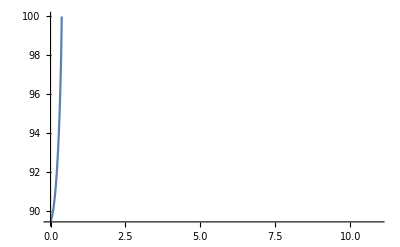

-Graphics-

-Graphics-

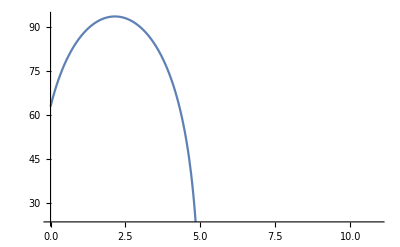

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

0.111389

0.381389

2.53073

12.5307

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[v1[t],t]
a1[t_]=D[v1[t],t]

t1=.111389

L=.22
A1=((4.75*10^(-3))^2)*Pi
P1=4.4*10^5
M0=0.6889
g=9.81

sol2=DSolve[{v'[t]==(2*A1(P1-P2))/(M0-ρ1*ve*A1*t)-g,v[0]==3.95012},v[t],t]
v2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[v2[t],t]+h1[t1]
a2[t_]=D[v2[t],t]



t2=.27

A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
ve=26.07680962
ρ1=1000


sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==41.0204},v[t],t]
v3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[v3[t],t]+h2[t2]
a3[t_]=D[v3[t],t]

t3=2.14934

ρ2=1.22
g=9.81
A2=((.06)^2)*Pi
c=0.8
M2=.1889
k=ρ2*A2/2

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[v4[t],t]
a4[t_]=D[v4[t],t]

t4=Solve[h4[t]==0,t]
vi4=Simplify[h4[t]/.t4[[1]]]


P1=4.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
M2=.1889
g=9.81
L=.22
P1=4.4*10^5
P2=10^5
ve=26.07680962
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
M2=.1889
ρ1=1000

Plot[h1[t],{t,0,10.91}]

Plot[v1[t],{t,0,10.91}]

Plot[a1[t],{t,0,10.91}]


Plot[h2[t],{t,0,10.91}]

Plot[v2[t],{t,0,10.91}]

Plot[a2[t],{t,0,10.91}]


Plot[h3[t],{t,0,10.91}]

Plot[v3[t],{t,0,10.91}]

Plot[a3[t],{t,0,10.91}]


Plot[h4[t]-h4[0],{t,0,5}]

Plot[v4[t],{t,0,10.91}]

Plot[a4[t],{t,0,10.91}]

t1=0.111389
t2=t1+.27
t3=t2+2.14934
t4=t3+10

h1com[t_]:=h1[t]/;t<t1
h2com[t_]:=h2sol[t]/;t1<t<t2
h3com[t_]:=h3sol[t]/;t2<t<t3
h4com[t_]:=h4sol[t]/;t3<t<t4
```

```mathematica
t1=0.111389
t2=.27
t3=t2+2.14934
t4=t3+8
```

0.111389

0.4

2.54934

10.5493

```mathematica
hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<t4
```

```mathematica
Function[t,h1[t]/;t<t1]
```

Function[t,h1[t]/;t<t1]

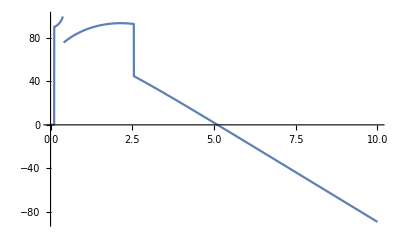

```mathematica
Plot[hcom[t],{t,0,10}]
```

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

-(g t^2)/2+(A1 P1 t^2)/(2 M0)

(-g M0+A1 P1)/M0

0.111389

0.22

0.0000708822

440000.

0.6889

9.81

{{v[t]→-(9.81 (-823651.+1.87193 P2-0.402663 ve ρ1+1. t ve ρ1+89704.4 Log[9718.94-1. t ve ρ1]-0.203874 P2 Log[9718.94-1. t ve ρ1]))/(ve ρ1)}}

-(9.81 (-823651.+1.87193 P2-0.402663 ve ρ1+1. t ve ρ1+89704.4 Log[9718.94-1. t ve ρ1]-0.203874 P2 Log[9718.94-1. t ve ρ1]))/(ve ρ1)

0.22+3.95012 t-4.905 t^2+(8.96001×10^6 t)/(ve ρ1)-(20.3637 P2 t)/(ve ρ1)+(8.55267×10^9 Log[9718.94-1. t ve ρ1])/(ve^2 ρ1^2)-(19437.9 P2 Log[9718.94-1. t ve ρ1])/(ve^2 ρ1^2)-(880000. t Log[9718.94-1. t ve ρ1])/(ve ρ1)+(2. P2 t Log[9718.94-1. t ve ρ1])/(ve ρ1)

-(9.81 (1. ve ρ1-(89704.4 ve ρ1)/(9718.94-1. t ve ρ1)+(0.203874 P2 ve ρ1)/(9718.94-1. t ve ρ1)))/(ve ρ1)

0.270507

0.0000708822

0.6889

26.0768

1000

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(3.13209 √M2 Tan[(0.3 (-10.4403 √c √k t+3.33333 √M2 ArcTan[(13.0968 √c √k)/(√M2)]))/(√M2)])/(√c √k)}}

(3.13209 √M2 Tan[(0.3 (-10.4403 √c √k t+3.33333 √M2 ArcTan[(13.0968 √c √k)/(√M2)]))/(√M2)])/(√c √k)

121.08-0.000273069 P2+(1. M2 Log[Cos[(3.13209 √c √k t)/(√M2)-1. ArcTan[(13.0968 √c √k)/(√M2)]]])/(c k)

-9.81 Sec[(0.3 (-10.4403 √c √k t+3.33333 √M2 ArcTan[(13.0968 √c √k)/(√M2)]))/(√M2)]^2

2.14934

1.22

9.81

0.0113097

0.8

0.1889

0.00689894

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))}}

-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))

121.08-0.000273069 P2+18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]

(19.62 ⅇ^(1.07074 t) (-1.+1. ⅇ^(1.07074 t)))/((1.+1. ⅇ^(1.07074 t))^2)-(19.62 ⅇ^(1.07074 t))/(1.+1. ⅇ^(1.07074 t))

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[121.08-0.000273069 P2+18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]==0,t]

ReplaceAll::reps: {121.08-0.000273069 P2+18.3238 t-34.2263 Log[1.+ⅇ^Times[«2»]]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

121.08-0.000273069 P2+18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]/.1. P2+125339. Log[1.+ⅇ^(1.07074 t)]==443404.+67103. t

440000.

0.0000708822

0.6889

0.1889

9.81

0.22

440000.

100000

26.0768

1.22

0.0113097

0.00689894

0.8

0.1889

1000

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

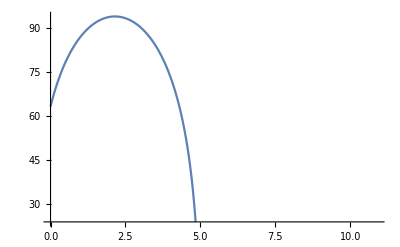

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

0.111389

0.381896

2.53124

12.5312

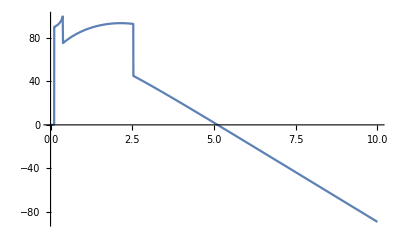

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[v1[t],t]
a1[t_]=D[v1[t],t]

t1=.111389

L=.22
A1=((4.75*10^(-3))^2)*Pi
P1=4.4*10^5
M0=0.6889
g=9.81

sol2=DSolve[{v'[t]==(2*A1(P1-P2))/(M0-ρ1*ve*A1*t)-g,v[0]==3.95012},v[t],t]
v2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[v2[t],t]+h1[t1]
a2[t_]=D[v2[t],t]



t2=0.2705069712

A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
ve=26.07680962
ρ1=1000


sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==41.0204},v[t],t]
v3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[v3[t],t]+h2[t2]
a3[t_]=D[v3[t],t]

t3=2.14934

ρ2=1.22
g=9.81
A2=((.06)^2)*Pi
c=0.8
M2=.1889
k=ρ2*A2/2

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[v4[t],t]+h3[t3]
a4[t_]=D[v4[t],t]

t4=Solve[h4[t]==0,t]
vi4=Simplify[h4[t]/.t4[[1]]]


P1=4.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M0=0.6889
M2=.1889
g=9.81
L=.22
P1=4.4*10^5
P2=10^5
ve=26.07680962
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
M2=.1889
ρ1=1000

Plot[h1[t],{t,0,10.91}]

Plot[v1[t],{t,0,10.91}]

Plot[a1[t],{t,0,10.91}]


Plot[h2[t],{t,0,10.91}]

Plot[v2[t],{t,0,10.91}]

Plot[a2[t],{t,0,10.91}]


Plot[h3[t],{t,0,10.91}]

Plot[v3[t],{t,0,10.91}]

Plot[a3[t],{t,0,10.91}]


Plot[h4[t]-h4[0],{t,0,5}]

Plot[v4[t],{t,0,10.91}]

Plot[a4[t],{t,0,10.91}]

t1=0.111389
t2=t1+0.2705069712
t3=t2+2.14934
t4=t3+10

hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<t4

Plot[hcom[t],{t,0,10}]
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
```

{{v[t]→35.4624 t}}

```mathematica
h1[t_]=Integrate[v1[t],t]
```

17.7312 t^2

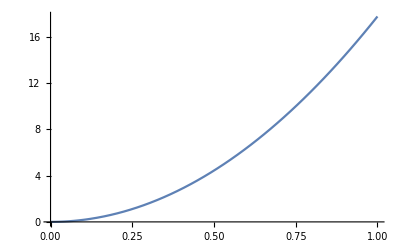

```mathematica
Plot[h1[t],{t,0,1}]
```

```mathematica
Clear[Mass]
```

```mathematica
Mass=DSolve[{M'[t]==-A1*ve*1000*t,M[0]==M0},M[t],t]
M[t_]=M[t]/.Mass[[1]]

tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[1]]]
```

DSolve::dsfun: 0.6889+0.924191 t^2 cannot be used as a function.

DSolve[{1.84838 t==-1.84838 t,True},0.6889+0.924191 t^2,t]

ReplaceAll::reps: {1.84838 t==-1.84838 t,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0.6889+0.924191 t^2/.{1.84838 t==-1.84838 t,True}

ReplaceAll::reps: {1.84838 t==-1.84838 t,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {1.84838 System`TSolveDump`X$5892[1]==-1.84838 System`TSolveDump`X$5892[1],True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {(90865421 System`TSolveDump`X$5892[1])/49159459==-(90865421 System`TSolveDump`X$5892[1])/49159459,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[(0.6889+0.924191 t^2/.{1.84838 t==-1.84838 t,True})==0,t]

ReplaceAll::reps: {(0.6889+0.924191 t^2/.{1.84838 t==-1.84838 t,True})==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-21.7869-9.81 t-26.0768 Log[0.372705-1. t]/.(0.6889+0.924191 t^2/.{t==0,True})==0

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[v1[t],t]
a1[t_]=D[v1[t],t]
```

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

-(g t^2)/2+(A1 P1 t^2)/(2 M0)

(-g M0+A1 P1)/M0

```mathematica
tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]
```

{{t→-(√2 √L)/(√(-g+(A1 P1)/M0))},{t→(√2 √L)/(√(-g+(A1 P1)/M0))}}

√2 √L √(-g+(A1 P1)/M0)

```mathematica
sol2=DSolve[{v'[t]==(2*A1(P1-P2))/(M0-ρ1*ve*A1*t)-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[v2[t],t]
a2[t_]=D[v2[t],t]
```

{{v[t]→(√2 √L √((-g M0+A1 P1)/M0) ve ρ1-g t ve ρ1+2 P1 Log[M0]-2 P2 Log[M0]-2 P1 Log[M0-A1 t ve ρ1]+2 P2 Log[M0-A1 t ve ρ1])/(ve ρ1)}}

(√2 √L √((-g M0+A1 P1)/M0) ve ρ1-g t ve ρ1+2 P1 Log[M0]-2 P2 Log[M0]-2 P1 Log[M0-A1 t ve ρ1]+2 P2 Log[M0-A1 t ve ρ1])/(ve ρ1)

(2 (P1-P2) t+√2 √L √(-g+(A1 P1)/M0) t ve ρ1-1/2 g t^2 ve ρ1+2 (P1-P2) t Log[M0]-2 (P1-P2) t Log[M0-A1 t ve ρ1]+(2 M0 (P1-P2) Log[M0-A1 t ve ρ1])/(A1 ve ρ1))/(ve ρ1)

(-g ve ρ1+(2 A1 P1 ve ρ1)/(M0-A1 t ve ρ1)-(2 A1 P2 ve ρ1)/(M0-A1 t ve ρ1))/(ve ρ1)

```mathematica
Mass=DSolve[{M'[t]==-A1*ve*1000*t,M[0]==M0},M[t],t]
M[t_]=M[t]/.Mass[[1]]
```

{{M[t]→M0-500 A1 t^2 ve}}

M0-500 A1 t^2 ve

```mathematica
tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[2]]]
```

{{t→-0.863371},{t→0.863371}}

-11.6901-81.9227 ⅈ

```mathematica
sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
```

{{v[t]→-51.8274 Tan[(1.42914+0.712572 ⅈ)+0.189282 t]}}

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]
```

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

```mathematica
sol2=DSolve[{v'[t]==(2*A1(P1-P2))/(M0-ρ1*ve*A1*t)-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]
```

{{v[t]→(-g t ve ρ1+ve vi1 ρ1+2 P1 Log[M0]-2 P2 Log[M0]-2 P1 Log[M0-A1 t ve ρ1]+2 P2 Log[M0-A1 t ve ρ1])/(ve ρ1)}}

(-g t ve ρ1+ve vi1 ρ1+2 P1 Log[M0]-2 P2 Log[M0]-2 P1 Log[M0-A1 t ve ρ1]+2 P2 Log[M0-A1 t ve ρ1])/(ve ρ1)

```mathematica
sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]
```

{{v[t]→-51.8274 Tan[(1.42914+0.712572 ⅈ)+0.189282 t]}}

-51.8274 Tan[(1.42914+0.712572 ⅈ)+0.189282 t]

```mathematica
sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)}}

-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)

```mathematica
h1[t_]=Integrate[v1[t],t]
```

-(g t^2)/2+(A1 P1 t^2)/(2 M0)

```mathematica
h2[t_]=Integrate[v2[t],t]
```

-(g t^2)/2+t vi1+(2 P1 t)/(ve ρ1)-(2 P2 t)/(ve ρ1)+(2 P1 t Log[M0])/(ve ρ1)-(2 P2 t Log[M0])/(ve ρ1)+(2 M0 P1 Log[M0-A1 t ve ρ1])/(A1 ve^2 ρ1^2)-(2 M0 P2 Log[M0-A1 t ve ρ1])/(A1 ve^2 ρ1^2)-(2 P1 t Log[M0-A1 t ve ρ1])/(ve ρ1)+(2 P2 t Log[M0-A1 t ve ρ1])/(ve ρ1)

```mathematica
h3[t_]=Integrate[v3[t],t]
```

(M2 Log[Cos[(√c √g √k t)/(√M2)-ArcTan[(√c √k vi2)/(√g √M2)]]])/(c k)

```mathematica
h4[t_]=Integrate[v4[t],t]
```

-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)

```mathematica
a1[t_]=D[v1[t],t]
```

(-g M0+A1 P1)/M0

```mathematica
a2[t_]=D[v2[t],t]
```

(-g ve ρ1+(2 A1 P1 ve ρ1)/(M0-A1 t ve ρ1)-(2 A1 P2 ve ρ1)/(M0-A1 t ve ρ1))/(ve ρ1)

```mathematica
a3[t_]=D[v3[t],t]
```

-g Sec[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)]^2

```mathematica
a4[t_]=D[v4[t],t]
```

-g Sech[(√c √g √k t)/(√M2)]^2

```mathematica
tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]
```

{{t→-(√2 √L)/(√(-g+(A1 P1)/M0))},{t→(√2 √L)/(√(-g+(A1 P1)/M0))}}

√2 √L √(-g+(A1 P1)/M0)

```mathematica
Mass=DSolve[{M'[t]==-A1*ve*1000*t,M[0]==M0},M[t],t]
M[t_]=M[t]/.Mass[[1]]
```

{{M[t]→M0-500 A1 t^2 ve}}

M0-500 A1 t^2 ve

```mathematica
tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[1]]]
```

{{t→-(√M0)/(10 √5 √A1 √ve)},{t→(√M0)/(10 √5 √A1 √ve)}}

√2 √L √(-g+(A1 P1)/M0)+(g √M0)/(10 √5 √A1 √ve)+(2 (P1-P2) Log[M0])/(ve ρ1)-(2 (P1-P2) Log[M0+(√A1 √M0 √ve ρ1)/(10 √5)])/(ve ρ1)

```mathematica
tsol3=Solve[v3[t]==0,t]
```

{{t→(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)+(g √M0)/(10 √5 √A1 √ve)+(2 (P1-P2) Log[M0])/(ve ρ1)-(2 (P1-P2) Log[M0+(√A1 √M0 √ve ρ1)/(10 √5)])/(ve ρ1)))/(√g √M2)])/(√c √g √k)}}

```mathematica
tsol4=Solve[h4[t]==0,t]
```

{{t→ConditionalExpression[(2 ⅈ √M2 π C[1])/(√c √g √k),C[1]∈ℤ]}}

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2 = 10^5
M0=0.6889
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2
```

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

```mathematica
tsol1
```

{{t→-0.111389},{t→0.111389}}

```mathematica
tsol2
```

{{t→-0.863371},{t→0.863371}}

```mathematica
tsol3
```

{{t→-1.84239}}

```mathematica
{{t->5.283118731643117 ArcTan[0.01929481512008381 (12.419788154296704-0.00009195224651039236 (440000.00000000006-P2))]}}
```

{{t→-1.84239}}

```mathematica
tsol4
```

{{t→ConditionalExpression[(0.+33.1948 ⅈ) C[1],C[1]∈ℤ]}}

```mathematica
vi2
```

-18.844

```mathematica
Plot[h3[t],{t,0,10.91}]
```

-Graphics-

```mathematica
Clear [M,tsol3]
```

```mathematica
M[t_]=M0-A1*ve*1000*t
tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[1]]]
```

0.6889-1.84838 t

{{t→0.372705}}

Indeterminate

```mathematica
v2[t]
```

0.0000383482 (-150402.-255814. t-680000. Log[0.6889-1.84838 t])